# Normalized Additional Velocity (NAV)

By Davi Rodrigues & Alejandro Hernandez-Arboleda
March, 2022

The method is described in detail in the paper:
  Normalized Additional Velocity: a fast sample analysis for dark matter or modified gravity models
  A.Hernandez-Arboleda, D.C. Rodrigues, A.Wojnar

## 0. Prelude

```mathematica
isBurkertWithGaussianPriors = True; (*Loads the Burkert data with Gaussian priors (True), or the fixed case (False)*)

SetDirectory @ NotebookDirectory[];
Needs @ "NAVbaseCode`";
<< "NAVoptions.wl";
Get["MDC14aux.mx", Path -> "AuxiliaryData"] // Quiet; (*If something goes wrong, this file will be generated*)

SetDirectory @ FileNameJoin[{NotebookDirectory[], "Output"}];

If[isBurkertWithGaussianPriors,
  exportBurkertIndividualResultsGaussian,
  (*else*)
  exportBurkertIndividualResultsFixed,
  (*if neither True or False*)
  Exit[]
];
```

## I. Observational NAV

## I.1. Kernel Density Estimation for the distribution

All RAR galaxies case:

Gaussian bandwidths from Silverman rule of thumb:   {0.0676207,0.0820401}

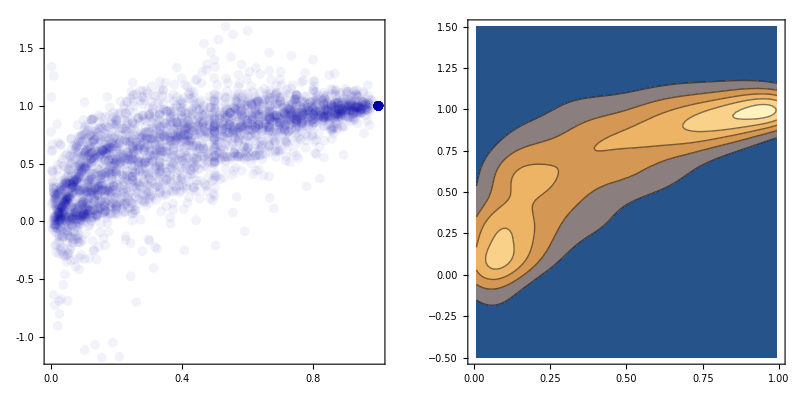

Only the bulgeless RAR galaxies:

Gaussian bandwidths from Silverman rule of thumb:   {0.0724175,0.0867233}

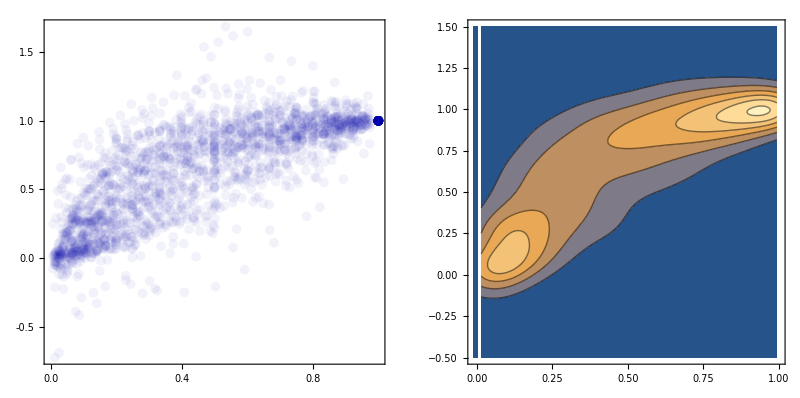

```mathematica
Clear[distributionSilverman, plotBlueZero, statusKDE];

distributionSilverman[dataForKDE_] := distributionSilverman[dataForKDE] = SmoothKernelDistribution[
  dataForKDE, 
  silvermanBw[dataForKDE], 
  "Gaussian", 
  MaxExtraBandwidths -> {{0,0}, {2,2}}, 
  (* No extension for the horizontal axis: there cannot be data lower than 0 and higher than 1,
   extension of 2 bandwidths in the vertical axis: relevant for a few models.*)
  InterpolationPoints -> 200
]; (*Apart from MaxExtraBandwidths and InterpolationPoints, these are the standard options for SmoothKernelDistribution*)
  

plotBlueZero[dataForKDE_, opts:OptionsPattern[]] := nListPlot[
  {dataForKDE}, 
  PlotMarkers -> {
    Graphics[{Darker[Blue],Opacity[0.05],Disk[]}, ImageSize -> 10], 
    Graphics[{Darker[Red],Opacity[0.3],Disk[]}, ImageSize -> 10]
  },
  opts,
  PlotRange -> {{0,1}, All},
  AspectRatio -> 1
];

statusKDE[dataForKDE_, {{xmin_, xmax_}, {ymin_, ymax_}}]:= Block[{},
  Echo[silvermanBw[dataForKDE], 
    "Gaussian bandwidths from Silverman rule of thumb: "
  ];
  Print@GraphicsRow[
    {
      plotBlueZero[dataForKDE], 
      ContourPlot[PDF[distributionSilverman[dataForKDE], {x, y}], {x, xmin, xmax}, {y, ymin, ymax}]
    }
  ]
];


(* SPECIFIC DEFINITIONS *)

Clear[gdRList, gdRListFlat];

gdRList[gdFunction_] := gdRList[gdFunction] = gdFunction[{nRad, δVms}][[#]] & /@ Range[175];
gdRListFlat[gdFunction_] := Flatten[gdRList[gdFunction], 1];

list2RARRot = gdRListFlat @ gdR;
list2RARRotNoBulge = gdRListFlat @ gdRBulgeless; 


(*EXECUTION*)

distRARRot = distributionSilverman[list2RARRot];
distRARRotNoBulge = distributionSilverman[list2RARRotNoBulge];

Echo["All RAR galaxies case:"];
statusKDE[list2RARRot, {{0, 1}, {-0.5, 1.5}}];
Echo["Only the bulgeless RAR galaxies:"];
statusKDE[list2RARRotNoBulge, {{-0.01,1}, {-0.5, 1.5}}];
```

## I.2. The 1σ and 2σ Highest Density Regions

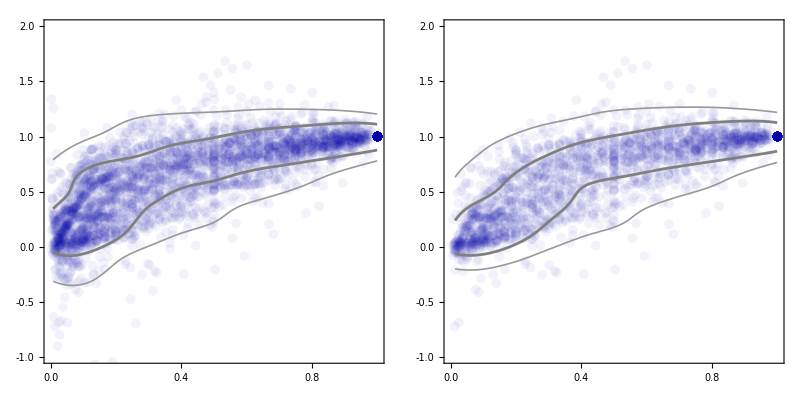

```mathematica
Clear[plotBlue, plotSigmaContours, plotBlueFunction];
(*list1LimitingPDFValues::usage = 
  "limitingPDFValues[data, {{xmin, xmax, xstep}, {ymin, ymax, ystep}}] provides {pdf1Sigma, pdf2sigma}}, \n " <>
  "where pdf1Sigma and pdf2Sigma are respectively the pdf values that limit the 1 or 2 Sigma highest denstiy region found from the KDE of the provided data. \n"<>
  "xmin, xmax, ymin and ymax set the region to be considered, while xstep and ystep the step size to be used to explore the distribution.";
*)  

oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];  
  
FindHDPDFValues::usage = "FindHDPDFValues[dist, probabilityList] yeilds a list of the PDF values that dermines the highest density probability regions, these PDF values correspond to the provided list of probabilities (probabilityList). FindHDPDFValues works for DataDistribution of any dimensions. It uses the discrete PDF table provided by dist[\"PDFValues\"], if higher resolution is desirable, increase the numbers of InterpolationPoints when generating the distribution (for instance, in SmoothKernelDistribution).";
FindHDPDFValues[dist_DataDistribution, probability_List] := Block[
  {pdfList, pdfSortList, cdfSortList, positionAtCdf, positionsAtPdf},
  pdfList = dist["PDFValues"];
  pdfSortList = Reverse @ Sort @ pdfList;
  cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList];
  positionAtCdf[prob_] := FirstPosition[cdfSortList, p_ /; p >= prob];
  positionsAtPdf = Flatten[positionAtCdf /@  probability];
  pdfSortList⟦positionsAtPdf⟧
];

plotSigmaContours[dataForContours_, limitingPdfValues_, {{xmin_, xmax_}, {ymin_, ymax_}}, options___]:= Block[
  {pdf}, 
  pdf[x_,y_] = PDF[distributionSilverman[dataForContours], {x, y}]; 
  ContourPlot[
    pdf[x, y],
    {x, xmin, xmax},
    {y, ymin, ymax},
    Contours -> limitingPdfValues, (*Can be the output from FindHDPDFValues*)
    ContourShading -> None, 
    ContourStyle -> {
      {Thickness[0.003], Lighter[Gray, 0.2]},
      {Thickness @ 0.005, Gray}
    },
    options
  ]
];

plotBlue[dataForBluePlot_, limitingPdfValeus_, {{xmin_, xmax_}, {ymin_, ymax_}}, options___] := Show[
  plotBlueZero[dataForBluePlot, options],
  plotSigmaContours[dataForBluePlot, limitingPdfValeus, {{xmin, xmax}, {ymin, ymax}}, PlotRange -> All]
];

(* SPECIFIC DEFINITIONS *)

ymin = -1.5;
ymax = 2.5;
xmin= 0;
xmax = 1;
xstep = 0.005;
ystep = 0.005;

oneAndTwoSigma = {oneSigmaProbability, twoSigmaProbability};
list1Limits = FindHDPDFValues[distRARRot, oneAndTwoSigma];
list1LimitsNoBulge = FindHDPDFValues[distRARRotNoBulge, oneAndTwoSigma];

plotBlueFunction = plotBlue[Sequence@@#, {{xmin, xmax - 0.001}, {-0.5, 1.5}}, PlotRange -> {{0, 1}, {-1, 2}}] & ;

(* EXECUTION *)

{plotBlueRAR, plotBlueRARNoBulge} = plotBlueFunction /@ {{list2RARRot, list1Limits}, {list2RARRotNoBulge, list1LimitsNoBulge}};

GraphicsRow[
  {plotBlueRAR, plotBlueRARNoBulge},
  0,
  ImageSize -> 800
]

Export["plotBlueRAR.pdf", plotBlueRAR];
Export["plotBlueRARNoBulge.pdf", plotBlueRARNoBulge];
```

Cell group comment: 
Considers the removal of Vobs data points with uncertainty larger than 10%.
Conclusion: no relevant impact and adds complications

Case with Bulge:

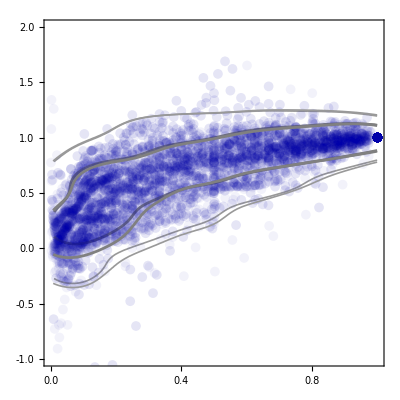

```mathematica
Clear[gdRListVel, gdRListVelFlat]
gdRListVel[gdFunction_] := gdRListVel[gdFunction] = gdFunction[{nRad, δVms, Vobs, δVobs}][[#]] & /@ Range[175];
gdRListVelFlat[gdFunction_] := Flatten[gdRListVel[gdFunction], 1];

list2RARRotVelAux = Select[gdRListVelFlat[gdR], #[[4]]/#[[3]] <  0.1 &] ; (*Includes only the velocity points with uncertainty lower than 10% of Vobs*)
list2RARRotVel = Drop[list2RARRotVelAuxᵀ, -2]ᵀ; (*Removes the columns on Vobs and δVobs*)

distRARRotVel = distributionSilverman[list2RARRotVel];

list1LimitsVel = FindHDPDFValues[distRARRotVel, oneAndTwoSigma];

plotBlueRARVel = plotBlueFunction[{list2RARRotVel, list1LimitsVel}] ; 
Show[plotBlueRARVel, plotBlueRAR]
```

Case without Bulge

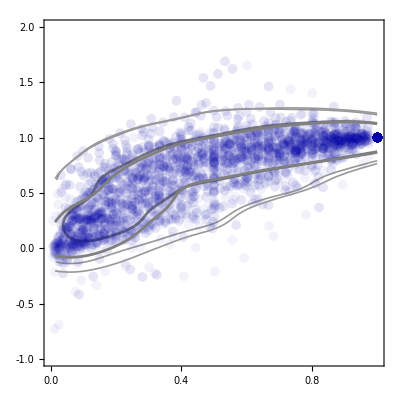

```mathematica
list2RARRotVelAuxNoBulge = Select[gdRListVelFlat[gdRBulgeless], #[[4]]/#[[3]] <  0.1 &] ; (*Includes only the velocity points with uncertainty lower than 10% of Vobs*)
list2RARRotVelNoBulge = Drop[list2RARRotVelAuxNoBulgeᵀ, -2]ᵀ; (*Removes the columns on Vobs and δVobs*)

distRARRotVelNoBulge = distributionSilverman[list2RARRotVelNoBulge];

list1LimitsVelNoBulge = FindHDPDFValues[distRARRotVelNoBulge, oneAndTwoSigma];

plotBlueRARVelNoBulge = plotBlueFunction[{list2RARRotVelNoBulge, list1LimitsVelNoBulge}] ; 
Show[plotBlueRARVelNoBulge, plotBlueRARNoBulge]
```

The plot below shows that the  excluded points most dense region is close to the galaxy center (as expectected, since there the observational velocity is typically close to zero, while the Vobs errors do not go to zero).

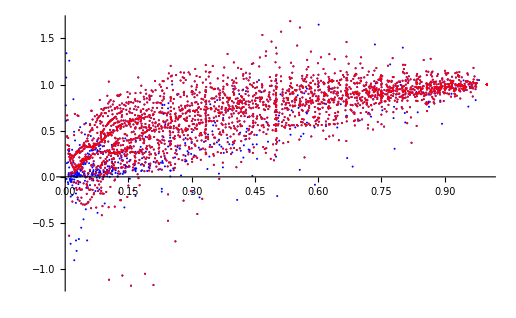

```mathematica
ListPlot[{ list2RARRot, list2RARRotVel}, PlotStyle-> {Blue, Red}]
```

The main differences appear in the lower bounds of the 1σ and 2σ regions, which get raised, in particular at r_n<0.2. The overall impact for our results is negligible. Since most of the excluded data points are close to the galactic center, in the bulgeless case the 1σ upper and lower limits get connected, which adds a nonnecessary computational complication and such case is artificial, since it depends on the choice of the 10% rejection limit).

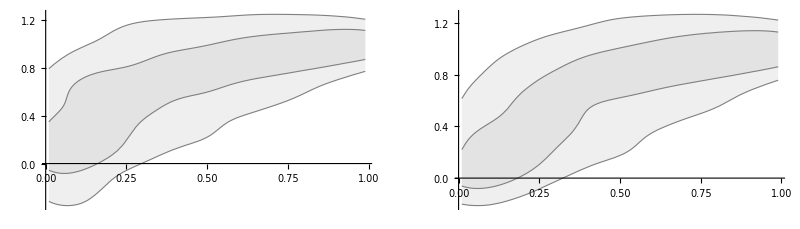

```mathematica
Clear[list1InterpSigmaCurves, plotSigmaRegions];
list1InterpSigmaCurves::usage = "list1InterpSigmaCurves[blueplot] provides a list of 4 interpolated curves in the following order:"<> 
    "{1σLowerLimit, 1σUpperLimit, 2σLowerLimit, 2σUpperLimit}. /n"<>
    "The plot to be provided (blueplot) can be generated by the function plotBlue.";
list1InterpSigmaCurves[plotblue_] := Block[
  {
    sigmaContoursList,
    curveSigma, 
    curveOrder, 
    curve2SigmaNeg, 
    curve1SigmaNeg, 
    curve1SigmaPlus, 
    curve2SigmaPlus
  },
  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ plotblue,
    Line[pts_] :> pts,
    Infinity
  ];
  curveSigma[n_] := Interpolation[
    Sort@sigmaContoursList⟦n⟧,
    Method -> "Spline", 
    InterpolationOrder-> 2
  ];
  curveOrder = Ordering @ Table[curveSigma[n][0.5], {n, 1, 4}];
  curve2SigmaNeg = curveSigma[curveOrder⟦1⟧];
  curve1SigmaNeg = curveSigma[curveOrder⟦2⟧];
  curve1SigmaPlus = curveSigma[curveOrder⟦3⟧];
  curve2SigmaPlus = curveSigma[curveOrder⟦4⟧];
  {
    curve1SigmaNeg,
    curve1SigmaPlus,
    curve2SigmaNeg, 
    curve2SigmaPlus
  }
];

plotSigmaRegions::usage = 
  "plotSigmaRegions[curvesSigma, xLimit1, xLimit2] yields a plot with the 1 and 2 sigma regions from xLimit1 to xLmit2. \n" <>
  "The standard values of xLimit1 and xLimit2 are 0.2 and 0.9. \n" <>
  "The input to be provided, curvesSigma, can be generated by list1InterpSigmaCurves.";
  
plotSigmaRegions[curvesSigma_, xLimit1_:0.01, xLimit2_:0.99] := Plot[
  {
    curvesSigma[[3]][r],
    curvesSigma[[1]][r],
    curvesSigma[[2]][r],
    curvesSigma[[4]][r]
  },
  {r, xLimit1, xLimit2},
  Filling -> {{1 -> {3}, GrayLevel[0.7]}, {2 -> {4}}},
  PlotStyle -> {{Thickness[0.002], Gray}, {Thickness @ 0.002, Gray}},
  FillingStyle -> {GrayLevel[0.7], Opacity @ 0.05}
];

(*EXECUTION*)

{plotSigmaRegionsRAR, plotSigmaRegionsRARNoBulge} = plotSigmaRegions[list1InterpSigmaCurves[#]] & /@ {plotBlueRAR, plotBlueRARNoBulge};

plotBackground[upperLimit_] := nPlot[
  100,
  {rn, 0, 1},
  PlotRange -> {{0, 1}, {-0.25, upperLimit}},
  AspectRatio -> (1 / 1.3),
  GridLines -> None, 
  Prolog -> {
    Dotted,
    Line @ {{0, 0}, {1, 0}},
    Gray,
    Opacity[0.2], 
    Rectangle[{0.001, -0.5},{0.2, upperLimit}],
    Rectangle[{0.9, -0.5},{0.999, upperLimit}]
  }
];

GraphicsRow[
  {plotSigmaRegionsRAR, plotSigmaRegionsRARNoBulge},
  ImageSize -> 800
]
```

### I.2.1. Exporting the σ regions into a almost-paper-ready table (uncomment to export the files)

```mathematica
Clear[exportSigmaList]
exportSigmaList::usage = "curvesSigmaList[listOfCurves, rnMin, rnMax, step] generates 1σ and 2σ limiting curves in a close-to-paper-ready formated table, /n"<>
  "with rMin < r < rMax, in steps provided by step (optional, 0.02 being standard). The listOfCurves can be generated by list1InterpSigmaCurves./n"<>
  "exportSigmaList does not exports any file, but prepares the list to be exported.";

exportSigmaList[list1IpSigmaCurves_, rnMin_, rnMax_, step_:0.025] := Block[
  {header, tab, rn, nF, tabAux},
  header = {"# rn", "1σLower", "1σUpper", "2σLower", "2σUpper"};
  nF := NumberForm[#, {4, 3}] &;
  tabAux = Table[list1IpSigmaCurves[[n]]@rn, {n, 4}];
  tab = Table[
    nF /@ Flatten[{rn, tabAux}],
    {rn, rnMin, rnMax, step} 
  ];
  Join[{header}, tab]
];

list1InterpCurvesRAR = list1InterpSigmaCurves[plotBlueRAR];
list1InterpCurvesRARNoBulge = list1InterpSigmaCurves[plotBlueRARNoBulge];

 
(*Export["sigmaRegionsRAR.csv", exportSigmaList[list1InterpCurvesRAR, 0.025, 1]];
Export["sigmaRegionsRARNoBulge.csv", exportSigmaList[list1InterpCurvesRARNoBulge, 0.025, 1]];*)
```

## I.3 NAV efficiency definition

```mathematica
δVobs1σL[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[1]][xn]; (*L stands for lower limit*)
δVobs1σU[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[2]][xn]; (*U stands for upper limit*)
δVobs2σL[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[3]][xn];
δVobs2σU[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[4]][xn];

positivePart[x_] := HeavisideTheta[x] x;

Clear[areaObs];
areaObs[numberOfSigmas_] := Which[
  numberOfSigmas == 1, NIntegrate[δVobs1σU[xn] - δVobs1σL[xn], {xn, 0.2, 0.9}],
  numberOfSigmas == 2, NIntegrate[δVobs2σU[xn] - δVobs2σL[xn], {xn, 0.2, 0.9}],
  True, Echo["Wrong number of sigmas specification. Aborting."]; Abort[]
];
  
efficiencyNAV[ModelSigmaL_, ModelSigmaU_, numberOfSigmas_Integer] := Block[ (*There is another efficiencyNAV function with different number of arguments.*)
  {
    areaIntersection,
    areaModelOut,
    xn, (*equivalent to rn, used to avoid definition clash*)
    δVobsL,
    δVobsU
  },
  
  Which[
    numberOfSigmas == 1, δVobsL = δVobs1σL; δVobsU = δVobs1σU,
    numberOfSigmas == 2, δVobsL = δVobs2σL; δVobsU = δVobs2σU,
    True, Echo["Wrong number of sigmas specification. Aborting."]; Abort[]
  ];
  
  areaIntersection = NIntegrate[
    Min[δVobsU[xn], ModelSigmaU[xn]] - Max[δVobsL[xn], ModelSigmaL[xn]],
    {xn, 0.2, 0.9}
  ] / areaObs[numberOfSigmas];
  
  areaModelOut = NIntegrate[
    positivePart[ModelSigmaU[xn] - δVobsU[xn]] + positivePart[δVobsL[xn] - ModelSigmaL[xn]],
    {xn, 0.2, 0.9}
  ]/ areaObs[numberOfSigmas];
  
  {areaIntersection - areaModelOut, areaIntersection, areaModelOut}
];

Clear @ efficiencyNAVtotal; (*There is another efficiencyNAVtotal function with different number of arguments.*)
efficiencyNAVtotal[ModelSigmaL1_, ModelSigmaU1_, ModelSigmaL2_, ModelSigmaU2_] := (
  efficiencyNAV[ModelSigmaL1, ModelSigmaU1, 1] + 
  efficiencyNAV[ModelSigmaL2, ModelSigmaU2, 2]
) / 2;
```

## II. Burkert

### II.1 Burkert definition and limiting cases

Using rcn for the normalized rc: rc/Rmax and rn for the normalized radius: r/Rmax, the mass and the additional normalized velocity can be them easily computed:

plotBurkertGrayRed:

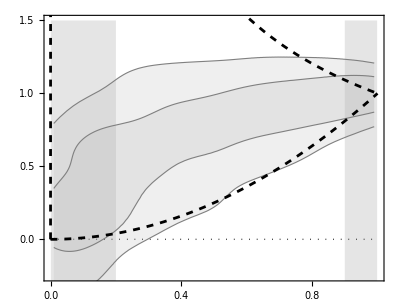

```mathematica
ρbrkt[rn_, rcn_, ρ0_] = ρ0/((1+rn/rcn)(1+rn^2/rcn^2));
Mbrkt[rn_, rcn_, ρ0_] = 4 π Rmax^3 Integrate[ρbrkt[rnprime,rcn,ρ0] rnprime^2,{rnprime,0,rn}, Assumptions-> {rn>0, rcn>0}];

VVbrkt[rn_, rcn_, ρ0_, Rmax_] = (G / Rmax) * Mbrkt[rn, rcn, ρ0] / rn;

δVbrkt[rn_, rcn_] = FullSimplify[
  VVbrkt[rn, rcn, ρ0, Rmax] / VVbrkt[1, rcn, ρ0, Rmax],
  Assumptions -> {0 < rn < 1, 0 < rcn < 1, 0 < Rmax}
];

plotBurkertGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVbrkt[rn, 1000], 
        δVbrkt[rn, 0.001]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotBurkertGrayRed:"];
Print@plotBurkertGrayRed;
```

### II.2. Burkert rcn Highest Density Regions

I want to find the values of rcn that best describe the n-sigma regions.

To this end, I have the find the minimum of the following integral (an extension of the χ^2 definition):

Performing the optimization.

rcn 1σ bounds:   {0.166051,0.606429}

rcn 2σ bounds:   {0.0989305,50.3425}

plotBurkertGlobalBestFit:

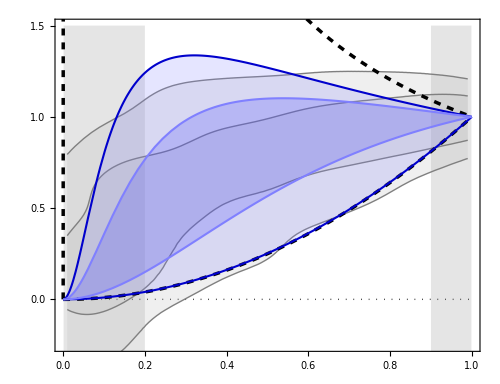

```mathematica
Clear[chi2Upper, chi2Lower];
chi2Upper[rcn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rcn_?NumberQ, nσ_]:= chi2Lower[rcn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.01;
rnEnd=0.99;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rcnUpper[2] = rcn /. NMinimize[{chi2Upper[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnUpper[1] = rcn /. NMinimize[{chi2Upper[rcn,1],rcn>0},{rcn,0,10}][[2]];
rcnLower[2] = rcn /. NMinimize[{chi2Lower[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnLower[1] = rcn /. NMinimize[{chi2Lower[rcn,1],rcn>0},{rcn,0,10}][[2]];

Echo[{rcnUpper[1], rcnLower[1]}, "rcn 1σ bounds: "];
Echo[{rcnUpper[2], rcnLower[2]}, "rcn 2σ bounds: "];

plotBurkertGlobalBestFit = Show[
  {
    plotBurkertGrayRed,
    Plot[
      {
        δVbrkt[rn, rcnUpper @ 2],
        δVbrkt[rn, rcnUpper @ 1],
        δVbrkt[rn, rcnLower @ 2],
        δVbrkt[rn, rcnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotBurkertGlobalBestFit:"];
Print@plotBurkertGlobalBestFit;

Export["plotBurkertGlobalBestFit.pdf", plotBurkertGlobalBestFit];
```

### II.3. Comparison with the rcn distribution found from the individual Burkert fits

The code below uses an older approach, but it works (compare with the Palatini approach)

1σ limits from individual fits:{0.107916, 0.49}

1σ limits from NAV method:{0.166051, 0.606429}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 1σ:

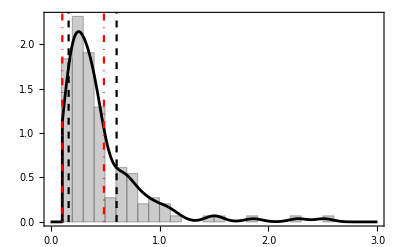

2σ limits from individual fits:{0.107916, 1.16}

2σ limits from NAV method:{0.0989305, 35.7141}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 2σ:

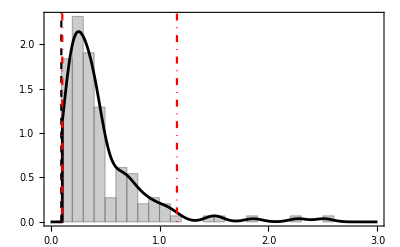

```mathematica
(*rcn values outside the upper and lower limits are not considered*)
(*The upper limit is important to eliminate those cases that are essentially infinity,
these also pose technical difficulties for the kernel density estimation.
The lower limit may be important since we have droppend all data with rn < 0.2,
There are galaxies that use the DM profile to do a quick rise of the rotation curve.*)

Clear[statusHistogram, nSigmas, rcnLowerLimit, rcnUpperLimit];

statusHistogram[nSigmas_, rcnLowerLimit_, rcnUpperLimit_]:= Block[{},
  Rmax[i_] := Last @ gd[Rad, i];
  rc[i_] := globalData⟦i, colrc⟧ ;
  posExcluded = Position[Table[galdataRAR @ n, {n, 1, 175}], {}];
  RmaxXrcAll = Table[{Rmax @ i, rc @ i}, {i, 1, 175}];
  RmaxXrc = Delete[RmaxXrcAll, posExcluded];
  rcnDataAll =  (Divide @@@ RmaxXrcAll)^-1;
  rcnData =  (Divide @@@ RmaxXrc)^-1;
  histoOptions =   Sequence @@ {
    Frame -> True, 
    Axes -> False, 
    ChartStyle -> Directive[EdgeForm[GrayLevel[0.4]], GrayLevel @ 0.8],
    FrameStyle -> Directive[GrayLevel[0.4], 16],
    PlotRangeClipping -> True,
    FrameTicks -> {{LinTicks, StripTickLabels@LinTicks2}, {LinTicks, StripTickLabels@LinTicks2}}
  };
  
  rcnDataWithoutOutliers = Select[rcnData, rcnLowerLimit < # < rcnUpperLimit &]; 
  dist = SmoothKernelDistribution[
    rcnDataWithoutOutliers, 
    silvermanBw[rcnDataWithoutOutliers], 
    MaxExtraBandwidths -> 0,
    InterpolationPoints -> 10^4
  ];

  pdfValuesForContours = Block[
    {
      positionAtCdf, oneSigmaProbability, twoSigmaProbability, positionsAtPdf, pdfList,
      pdfSortList, cdfSortList
    },
    oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
    twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];
    pdfList = Table[
      PDF[dist,x],
      {x, 0, 3, 0.01}
    ];
    pdfSortList = Reverse @ Sort @ Flatten @ pdfList;
    cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList] ;
    positionAtCdf[probability_] := FirstPosition[cdfSortList, p_ /; GreaterEqual[p, probability]];
    positionsAtPdf = Flatten @ Map[positionAtCdf, {oneSigmaProbability, twoSigmaProbability}];
    pdfSortList⟦positionsAtPdf⟧
  ];

  sigmaContoursPlot = ContourPlot[
    PDF[dist,x],
    {x, 0, 3},
    {y,0, 2},
    Contours -> pdfValuesForContours, 
    PlotRange -> {{0., 3}, All}
  ];

  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ sigmaContoursPlot,
    Line[pts_] :> pts,
    Infinity
  ];

  maxPDF = x /. Last @ Maximize[PDF[dist, x], x];

  rcnRootsSigma[i_] := Quiet[
    FindRoot[
      PDF[dist,x]==pdfValuesForContours[[i]], #
    ] & /@ {{x,0,maxPDF}, {x,maxPDF,3}},
    FindRoot::brmp
  ];

  {rcnLow @ 1, rcnHigh @ 1} = x /. rcnRootsSigma[1];
  {rcnLow @ 2, rcnHigh @ 2} = x /. Quiet[rcnRootsSigma[2], FindRoot::brmp];

  lines = {
    Dashed, 
    Thickness @ 0.004, 
    Line @ {{rcnUpper @ nSigmas, 0}, {rcnUpper @ nSigmas, 100}},
    Line @ {{rcnLower @ nSigmas, 0}, {rcnLower @ nSigmas, 100}}
  };

  lines2= {
    Red,
    DotDashed, 
    Thickness @ 0.004, 
    Line @ {{rcnLow @ nSigmas, 0}, {rcnLow @ nSigmas, 100}},
    Line @ {{rcnHigh @ nSigmas, 0}, {rcnHigh @ nSigmas, 100}}
  };

  rcnDistributionHistogram := Histogram[
    rcnDataWithoutOutliers,
    {0.1}, 
    "PDF", 
    PlotRange -> {{0, 3}, All},
    Frame -> True, 
    Axes -> False, 
    Epilog -> {lines, lines2}, 
    histoOptions
  ];

  Echo[ToString@nSigmas <>"σ limits from individual fits:" <> ToString@{rcnLow@nSigmas, rcnHigh@nSigmas}];
  Echo[ToString@nSigmas <>"σ limits from NAV method:" <> ToString@{rcnUpper@nSigmas, rcnLower@nSigmas}];
  Echo["Lower and upper rcn limits used for the individual Burkert fits: " <> ToString[{rcnLowerLimit, rcnUpperLimit}]];
  Echo["rcnDistributionHistogram for "<> ToString@nSigmas <>"σ:"];
  Print@Show[{rcnDistributionHistogram, nPlot[PDF[dist,x], {x,0,3}, PlotRange -> All]}]
];

statusHistogram[1, 0, 100];

statusHistogram[2,0,100];
```

## III. NFW

### III.1 NFW definition and limiting cases

Using rsn for the normalized rs: rs/Rmax and rn for the normalized radius: r/Rmax, the mass and the additional normalized velocity can be them easily computed:

```mathematica
ρnfw[rn_, rsn_, ρs_] = ρs/(rn/rsn(1+rn/rsn)^2);
Mnfw[rn_, rsn_, ρs_] = 4 π Rmax^3 Integrate[ρnfw[rnprime, rsn, ρs] rnprime^2, {rnprime, 0, rn}, Assumptions-> {rn>0, rsn>0}];

VVnfw[rn_, rsn_, ρs_, Rmax_] = (G / Rmax) * Mnfw[rn, rsn, ρs] / rn;

δVnfw[rn_, rsn_] = FullSimplify[
  VVnfw[rn, rsn, ρs, Rmax] / VVnfw[1, rsn, ρs, Rmax],
  Assumptions -> {0 < rn < 1, 0 < rsn < 1, 0 < Rmax}
];
```

plotNFWGrayRed:

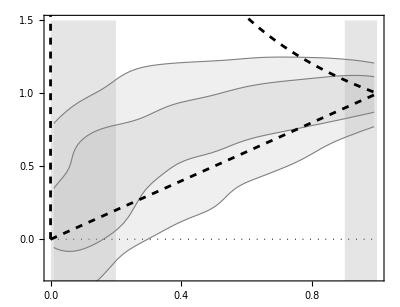

```mathematica
plotNFWGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVnfw[rn, 1000], 
        δVnfw[rn, 0.001]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotNFWGrayRed:"];
Print@plotNFWGrayRed;
```

### II.2. NFW rsn Highest Density Regions

I want to find the values of rsn that best describe the n-sigma regions.

To this end, I have the find the minimum of the following integral (an extension of the χ^2 definition):

Performing the optimization.

rsn 1σ bounds:   {0.288288,9.87941}

rsn 2σ bounds:   {0.143492,3107.48}

plotNFWGlobalBestFit:

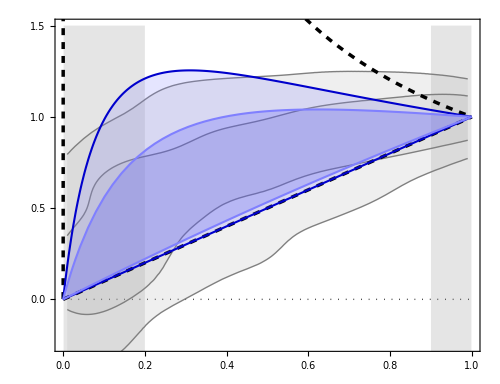

```mathematica
Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVnfw[rn,rsn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rsn_?NumberQ, nσ_]:= chi2Lower[rsn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVnfw[rn,rsn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.01;
rnEnd=0.99;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rsnUpper[2] = rsn /. NMinimize[{chi2Upper[rsn,2], rsn > 0}, {rsn, 0, 1}][[2]];
rsnUpper[1] = rsn /. NMinimize[{chi2Upper[rsn,1], rsn > 0}, {rsn, 0, 1}][[2]];
rsnLower[2] = rsn /. NMinimize[{chi2Lower[rsn,2], rsn > 0}, {rsn, 10, 1000}][[2]];
rsnLower[1] = rsn /. NMinimize[{chi2Lower[rsn,1], rsn > 0}, {rsn, 10, 1000}][[2]];

Echo[{rsnUpper[1], rsnLower[1]}, "rsn 1σ bounds: "];
Echo[{rsnUpper[2], rsnLower[2]}, "rsn 2σ bounds: "];

plotNFWGlobalBestFit = Show[
  {
    plotNFWGrayRed,
    Plot[
      {
        δVnfw[rn, rsnUpper @ 2],
        δVnfw[rn, rsnUpper @ 1],
        δVnfw[rn, rsnLower @ 2],
        δVnfw[rn, rsnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotNFWGlobalBestFit:"];
Print@plotNFWGlobalBestFit;

Export["plotNFWGlobalBestFit.pdf", plotNFWGlobalBestFit];
```

### III.3. Comparison with the rsn distribution found from the individual NFW fits

#### Fixed mass-to-light ratios as 0.5 and 0.6. Linear scale in rs.

1σ limits from individual fits:{0.148732, 1.98}

1σ limits from NAV method:{0.288288, 9.87941}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 1σ:

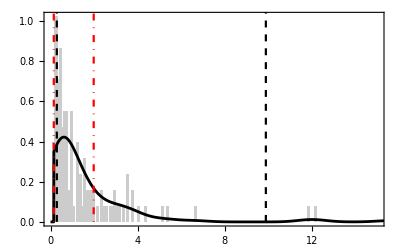

2σ limits from individual fits:{0.148732, 5.75316}

2σ limits from NAV method:{0.143492, 3107.48}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 2σ:

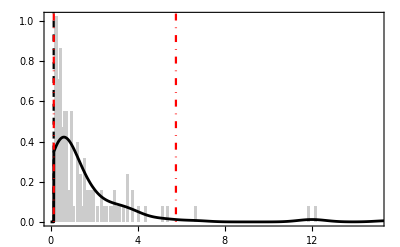

```mathematica
(*rcn values outside the upper and lower limits are not considered*)
(*The upper limit is important to eliminate those cases that are essentially infinity,
these also pose technical difficulties for the kernel density estimation.
The lower limit may be important since we have droppend all data with rn < 0.2,
There are galaxies that use the DM profile to do a quick rise of the rotation curve.*)

Clear[statusHistogram, nSigmas, rsnLowerLimit, rsnUpperLimit];

colrs = colrc; (*then col number of rc is the same of rs*)

statusHistogramNfwFixed[nSigmas_, rsnLowerLimit_, rsnUpperLimit_]:= Block[{},
  Rmax[i_] := Last @ gd[Rad, i];
  rs[i_] := globalDataNfwFixed⟦i, colrs⟧ ;
  posExcluded = Position[Table[galdataRAR @ n, {n, 1, 175}], {}];
  RmaxXrsAll = Table[{Rmax @ i, rs @ i}, {i, 1, 175}];
  RmaxXrs = Delete[RmaxXrsAll, posExcluded];
  rsnDataAll =  (Divide @@@ RmaxXrsAll)^-1;
  rsnData =  (Divide @@@ RmaxXrs)^-1;  (*IMPORTANT INTRODUCED LOG HERE*)
  histoOptions =   Sequence @@ {
    Frame -> True, 
    Axes -> False, 
    ChartStyle -> Directive[EdgeForm[GrayLevel[0.4]], GrayLevel @ 0.8],
    FrameStyle -> Directive[GrayLevel[0.4], 16],
    PlotRangeClipping -> True,
    FrameTicks -> {{LinTicks, StripTickLabels@LinTicks2}, {LinTicks, StripTickLabels@LinTicks2}}
  };
  
  rsnDataWithoutOutliers = Select[rsnData, rsnLowerLimit < # < rsnUpperLimit &]; 
  dist = SmoothKernelDistribution[
    rsnDataWithoutOutliers, 
    silvermanBw[rsnDataWithoutOutliers], 
    MaxExtraBandwidths -> 0,
    InterpolationPoints -> 10^4
  ];

  pdfValuesForContours = Block[
    {
      positionAtCdf, oneSigmaProbability, twoSigmaProbability, positionsAtPdf, pdfList,
      pdfSortList, cdfSortList
    },
    oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
    twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];
    pdfList = Table[
      PDF[dist, x],
      {x, 0, 20, 0.01}
    ];
    pdfSortList = Reverse @ Sort @ Flatten @ pdfList;
    cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList] ;
    positionAtCdf[probability_] := FirstPosition[cdfSortList, p_ /; GreaterEqual[p, probability]];
    positionsAtPdf = Flatten @ Map[positionAtCdf, {oneSigmaProbability, twoSigmaProbability}];
    pdfSortList⟦positionsAtPdf⟧
  ];

  sigmaContoursPlot = ContourPlot[
    PDF[dist, x],
    {x, 0, 20},
    {y, 0, 2},
    Contours -> pdfValuesForContours, 
    PlotRange -> {{0, 20}, All}
  ];

  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ sigmaContoursPlot,
    Line[pts_] :> pts,
    Infinity
  ];

  maxPDF = x /. Last @ Maximize[PDF[dist, x], x];

  rsnRootsSigma[i_] := Quiet[
    FindRoot[
      PDF[dist, x] == pdfValuesForContours[[i]], #
    ] & /@ {{x, 0, maxPDF}, {x, maxPDF, 20}},
    FindRoot::brmp
  ];

  {rsnLow @ 1, rsnHigh @ 1} = x /. rsnRootsSigma[1];
  {rsnLow @ 2, rsnHigh @ 2} = x /. Quiet[rsnRootsSigma[2], FindRoot::brmp];

  lines = {
    Dashed, 
    Thickness @ 0.004, 
    Line @ {{rsnUpper @ nSigmas, 0}, { rsnUpper @ nSigmas, 20}},
    Line @ {{rsnLower @ nSigmas, 0}, {rsnLower @ nSigmas, 20}}
  };

  lines2= {
    Red,
    DotDashed, 
    Thickness @ 0.004, 
    Line @ {{rsnLow @ nSigmas, 0}, {rsnLow @ nSigmas, 20}},
    Line @ {{rsnHigh @ nSigmas, 0}, {rsnHigh @ nSigmas, 20}}
  };

  rsnDistributionHistogram := Histogram[
    rsnDataWithoutOutliers,
    {0.1}, 
    "PDF", 
    PlotRange -> {{0, 15}, All},
    Frame -> True, 
    Axes -> False, 
    Epilog -> {lines, lines2}, 
    histoOptions
  ];

  Echo[ToString@nSigmas <>"σ limits from individual fits:" <> ToString@{rsnLow@nSigmas, rsnHigh@nSigmas}];
  Echo[ToString@nSigmas <>"σ limits from NAV method:" <> ToString@{rsnUpper@nSigmas, rsnLower@nSigmas}];
  Echo["Lower and upper rcn limits used for the individual Burkert fits: " <> ToString[{rsnLowerLimit, rsnUpperLimit}]];
  Echo["rcnDistributionHistogram for "<> ToString@nSigmas <>"σ:"];
  Print@Show[{rsnDistributionHistogram, nPlot[PDF[dist, x], {x, 0, 20}, PlotRange -> All]}]
];

statusHistogramNfwFixed[1, 0, 100];

statusHistogramNfwFixed[2, 0, 100];
```

#### Gaussian mass-to-light ratios, 0.5 and 0.6. Linear scale in rs.

1σ limits from individual fits:{0.00440529, 2.04}

1σ limits from NAV method:{0.288288, 9.87941}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 1σ:

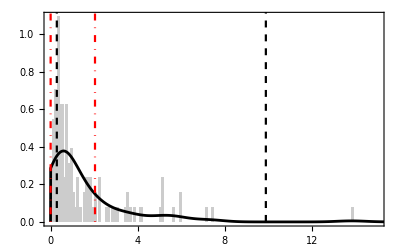

2σ limits from individual fits:{0.00440529, 7.02}

2σ limits from NAV method:{0.143492, 3106.97}

Lower and upper rcn limits used for the individual Burkert fits: {0, 100}

rcnDistributionHistogram for 2σ:

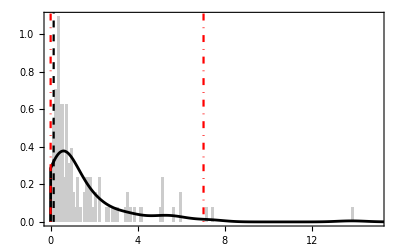

```mathematica
(*rcn values outside the upper and lower limits are not considered*)
(*The upper limit is important to eliminate those cases that are essentially infinity,
these also pose technical difficulties for the kernel density estimation.
The lower limit may be important since we have droppend all data with rn < 0.2,
There are galaxies that use the DM profile to do a quick rise of the rotation curve.*)

Clear[statusHistogram, nSigmas, rsnLowerLimit, rsnUpperLimit];

colrs = colrc; (*then col number of rc is the same of rs*)

statusHistogramNfwFixed[nSigmas_, rsnLowerLimit_, rsnUpperLimit_]:= Block[{},
  Rmax[i_] := Last @ gd[Rad, i];
  rs[i_] := globalDataNfwGY⟦i, colrs⟧ ;
  posExcluded = Position[Table[galdataRAR @ n, {n, 1, 175}], {}];
  RmaxXrsAll = Table[{Rmax @ i, rs @ i}, {i, 1, 175}];
  RmaxXrs = Delete[RmaxXrsAll, posExcluded];
  rsnDataAll =  (Divide @@@ RmaxXrsAll)^-1;
  rsnData =  (Divide @@@ RmaxXrs)^-1;  (*IMPORTANT INTRODUCED LOG HERE*)
  histoOptions =   Sequence @@ {
    Frame -> True, 
    Axes -> False, 
    ChartStyle -> Directive[EdgeForm[GrayLevel[0.4]], GrayLevel @ 0.8],
    FrameStyle -> Directive[GrayLevel[0.4], 16],
    PlotRangeClipping -> True,
    FrameTicks -> {{LinTicks, StripTickLabels@LinTicks2}, {LinTicks, StripTickLabels@LinTicks2}}
  };
  
  rsnDataWithoutOutliers = Select[rsnData, rsnLowerLimit < # < rsnUpperLimit &]; 
  dist = SmoothKernelDistribution[
    rsnDataWithoutOutliers, 
    silvermanBw[rsnDataWithoutOutliers], 
    MaxExtraBandwidths -> 0,
    InterpolationPoints -> 10^4
  ];

  pdfValuesForContours = Block[
    {
      positionAtCdf, oneSigmaProbability, twoSigmaProbability, positionsAtPdf, pdfList,
      pdfSortList, cdfSortList
    },
    oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
    twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];
    pdfList = Table[
      PDF[dist, x],
      {x, 0, 20, 0.01}
    ];
    pdfSortList = Reverse @ Sort @ Flatten @ pdfList;
    cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList] ;
    positionAtCdf[probability_] := FirstPosition[cdfSortList, p_ /; GreaterEqual[p, probability]];
    positionsAtPdf = Flatten @ Map[positionAtCdf, {oneSigmaProbability, twoSigmaProbability}];
    pdfSortList⟦positionsAtPdf⟧
  ];

  sigmaContoursPlot = ContourPlot[
    PDF[dist, x],
    {x, 0, 20},
    {y, 0, 2},
    Contours -> pdfValuesForContours, 
    PlotRange -> {{0, 20}, All}
  ];

  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ sigmaContoursPlot,
    Line[pts_] :> pts,
    Infinity
  ];

  maxPDF = x /. Last @ Maximize[PDF[dist, x], x];

  rsnRootsSigma[i_] := Quiet[
    FindRoot[
      PDF[dist, x] == pdfValuesForContours[[i]], #
    ] & /@ {{x, 0, maxPDF}, {x, maxPDF, 20}},
    FindRoot::brmp
  ];

  {rsnLow @ 1, rsnHigh @ 1} = x /. rsnRootsSigma[1];
  {rsnLow @ 2, rsnHigh @ 2} = x /. Quiet[rsnRootsSigma[2], FindRoot::brmp];

  lines = {
    Dashed, 
    Thickness @ 0.004, 
    Line @ {{rsnUpper @ nSigmas, 0}, { rsnUpper @ nSigmas, 20}},
    Line @ {{rsnLower @ nSigmas, 0}, {rsnLower @ nSigmas, 20}}
  };

  lines2= {
    Red,
    DotDashed, 
    Thickness @ 0.004, 
    Line @ {{rsnLow @ nSigmas, 0}, {rsnLow @ nSigmas, 20}},
    Line @ {{rsnHigh @ nSigmas, 0}, {rsnHigh @ nSigmas, 20}}
  };

  rsnDistributionHistogram := Histogram[
    rsnDataWithoutOutliers,
    {0.1}, 
    "PDF", 
    PlotRange -> {{0, 15}, All},
    Frame -> True, 
    Axes -> False, 
    Epilog -> {lines, lines2}, 
    histoOptions
  ];

  Echo[ToString@nSigmas <>"σ limits from individual fits:" <> ToString@{rsnLow@nSigmas, rsnHigh@nSigmas}];
  Echo[ToString@nSigmas <>"σ limits from NAV method:" <> ToString@{rsnUpper@nSigmas, rsnLower@nSigmas}];
  Echo["Lower and upper rcn limits used for the individual Burkert fits: " <> ToString[{rsnLowerLimit, rsnUpperLimit}]];
  Echo["rcnDistributionHistogram for "<> ToString@nSigmas <>"σ:"];
  Print@Show[{rsnDistributionHistogram, nPlot[PDF[dist, x], {x, 0, 20}, PlotRange -> All]}]
];

statusHistogramNfwFixed[1, 0, 100];

statusHistogramNfwFixed[2, 0, 100];
```

#### Fixed mass-to-light ratios as 0.5 and 0.6. Log scale in rs.

1σ limits from individual fits:{-0.827594, 0.788315}

1σ limits from NAV method:{-0.540174, 0.994731}

Lower and upper rcn limits used for the individual Burkert fits: {-1, 4}

rcnDistributionHistogram for 1σ:

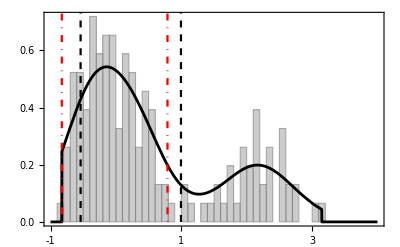

2σ limits from individual fits:{-0.827594, 2.81167}

2σ limits from NAV method:{-0.843173, 3.49234}

Lower and upper rcn limits used for the individual Burkert fits: {-1, 4}

rcnDistributionHistogram for 2σ:

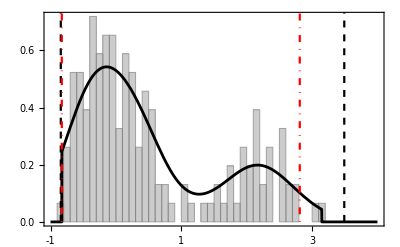

```mathematica
(*rcn values outside the upper and lower limits are not considered*)
(*The upper limit is important to eliminate those cases that are essentially infinity,
these also pose technical difficulties for the kernel density estimation.
The lower limit may be important since we have droppend all data with rn < 0.2,
There are galaxies that use the DM profile to do a quick rise of the rotation curve.*)

Clear[statusHistogram, nSigmas, rsnLowerLimit, rsnUpperLimit];

colrs = colrc; (*then col number of rc is the same of rs*)

statusHistogramNfwFixed[nSigmas_, rsnLowerLimit_, rsnUpperLimit_]:= Block[{},
  Rmax[i_] := Last @ gd[Rad, i];
  rs[i_] := globalDataNfwFixed⟦i, colrs⟧ ;
  posExcluded = Position[Table[galdataRAR @ n, {n, 1, 175}], {}];
  RmaxXrsAll = Table[{Rmax @ i, rs @ i}, {i, 1, 175}];
  RmaxXrs = Delete[RmaxXrsAll, posExcluded];
  rsnDataAll =  (Divide @@@ RmaxXrsAll)^-1;
  rsnData =  Log10 @ ((Divide @@@ RmaxXrs)^-1);  (*IMPORTANT INTRODUCED LOG HERE*)
  histoOptions =   Sequence @@ {
    Frame -> True, 
    Axes -> False, 
    ChartStyle -> Directive[EdgeForm[GrayLevel[0.4]], GrayLevel @ 0.8],
    FrameStyle -> Directive[GrayLevel[0.4], 16],
    PlotRangeClipping -> True,
    FrameTicks -> {{LinTicks, StripTickLabels@LinTicks2}, {LinTicks, StripTickLabels@LinTicks2}}
  };
  
  rsnDataWithoutOutliers = Select[rsnData, rsnLowerLimit < # < rsnUpperLimit &]; 
  dist = SmoothKernelDistribution[
    rsnDataWithoutOutliers, 
    silvermanBw[rsnDataWithoutOutliers], 
    MaxExtraBandwidths -> 0,
    InterpolationPoints -> 10^4
  ];

  pdfValuesForContours = Block[
    {
      positionAtCdf, oneSigmaProbability, twoSigmaProbability, positionsAtPdf, pdfList,
      pdfSortList, cdfSortList
    },
    oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
    twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];
    pdfList = Table[
      PDF[dist, x],
      {x, -1, 4, 0.01}
    ];
    pdfSortList = Reverse @ Sort @ Flatten @ pdfList;
    cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList] ;
    positionAtCdf[probability_] := FirstPosition[cdfSortList, p_ /; GreaterEqual[p, probability]];
    positionsAtPdf = Flatten @ Map[positionAtCdf, {oneSigmaProbability, twoSigmaProbability}];
    pdfSortList⟦positionsAtPdf⟧
  ];

  sigmaContoursPlot = ContourPlot[
    PDF[dist, x],
    {x, -1, 4},
    {y, 0, 2},
    Contours -> pdfValuesForContours, 
    PlotRange -> {{-1, 4}, All}
  ];

  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ sigmaContoursPlot,
    Line[pts_] :> pts,
    Infinity
  ];

  maxPDF = x /. Last @ Maximize[PDF[dist, x], x];

  rsnRootsSigma[i_] := Quiet[
    FindRoot[
      PDF[dist, x] == pdfValuesForContours[[i]], #
    ] & /@ {{x, -1, maxPDF}, {x, maxPDF, 4}},
    FindRoot::brmp
  ];

  {rsnLow @ 1, rsnHigh @ 1} = x /. rsnRootsSigma[1];
  {rsnLow @ 2, rsnHigh @ 2} = x /. Quiet[rsnRootsSigma[2], FindRoot::brmp];

  lines = {
    Dashed, 
    Thickness @ 0.004, 
    Line @ {{Log10 @ rsnUpper @ nSigmas, 0}, {Log10 @ rsnUpper @ nSigmas, 100}},
    Line @ {{Log10 @ rsnLower @ nSigmas, 0}, {Log10 @ rsnLower @ nSigmas, 100}}
  };

  lines2= {
    Red,
    DotDashed, 
    Thickness @ 0.004, 
    Line @ {{rsnLow @ nSigmas, 0}, {rsnLow @ nSigmas, 100}},
    Line @ {{rsnHigh @ nSigmas, 0}, {rsnHigh @ nSigmas, 100}}
  };

  rsnDistributionHistogram := Histogram[
    rsnDataWithoutOutliers,
    {0.1}, 
    "PDF", 
    PlotRange -> {{-1, 4}, All},
    Frame -> True, 
    Axes -> False, 
    Epilog -> {lines, lines2}, 
    histoOptions
  ];

  Echo[ToString@nSigmas <>"σ limits from individual fits:" <> ToString@{rsnLow@nSigmas, rsnHigh@nSigmas}];
  Echo[ToString@nSigmas <>"σ limits from NAV method:" <> ToString@{Log10 @ rsnUpper@nSigmas, Log10 @ rsnLower@nSigmas}];
  Echo["Lower and upper rcn limits used for the individual Burkert fits: " <> ToString[{rsnLowerLimit, rsnUpperLimit}]];
  Echo["rcnDistributionHistogram for "<> ToString@nSigmas <>"σ:"];
  Print@Show[{rsnDistributionHistogram, nPlot[PDF[dist, x], {x, -1, 4}, PlotRange -> All]}]
];

statusHistogramNfwFixed[1, -1, 4];

statusHistogramNfwFixed[2,-1, 4];
```

#### Gaussian mass-to-light ratios, 0.5 and 0.6. Log scale in rs.

1σ limits from individual fits:{-0.892563, 0.865178}

1σ limits from NAV method:{-0.540174, 0.994731}

Lower and upper rcn limits used for the individual Burkert fits: {-1, 4}

rcnDistributionHistogram for 1σ:

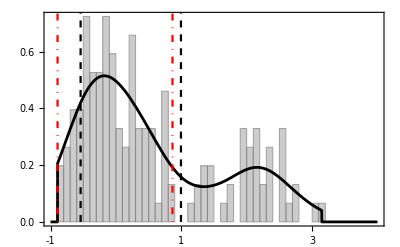

2σ limits from individual fits:{-0.892563, 2.66081}

2σ limits from NAV method:{-0.843173, 3.49234}

Lower and upper rcn limits used for the individual Burkert fits: {-1, 4}

rcnDistributionHistogram for 2σ:

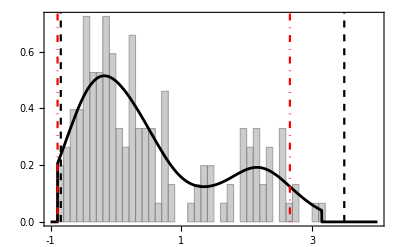

```mathematica
(*rcn values outside the upper and lower limits are not considered*)
(*The upper limit is important to eliminate those cases that are essentially infinity,
these also pose technical difficulties for the kernel density estimation.
The lower limit may be important since we have droppend all data with rn < 0.2,
There are galaxies that use the DM profile to do a quick rise of the rotation curve.*)

Clear[statusHistogram, nSigmas, rsnLowerLimit, rsnUpperLimit];

colrs = colrc; (*then col number of rc is the same of rs*)

statusHistogramNfwGY[nSigmas_, rsnLowerLimit_, rsnUpperLimit_]:= Block[{},
  Rmax[i_] := Last @ gd[Rad, i];
  rs[i_] := globalDataNfwGY⟦i, colrs⟧ ;
  posExcluded = Position[Table[galdataRAR @ n, {n, 1, 175}], {}];
  RmaxXrsAll = Table[{Rmax @ i, rs @ i}, {i, 1, 175}];
  RmaxXrs = Delete[RmaxXrsAll, posExcluded];
  rsnDataAll =  (Divide @@@ RmaxXrsAll)^-1;
  rsnData =  Log10 @ ((Divide @@@ RmaxXrs)^-1);  (*IMPORTANT INTRODUCED LOG HERE*)
  histoOptions =   Sequence @@ {
    Frame -> True, 
    Axes -> False, 
    ChartStyle -> Directive[EdgeForm[GrayLevel[0.4]], GrayLevel @ 0.8],
    FrameStyle -> Directive[GrayLevel[0.4], 16],
    PlotRangeClipping -> True,
    FrameTicks -> {{LinTicks, StripTickLabels@LinTicks2}, {LinTicks, StripTickLabels@LinTicks2}}
  };
  
  rsnDataWithoutOutliers = Select[rsnData, rsnLowerLimit < # < rsnUpperLimit &]; 
  dist = SmoothKernelDistribution[
    rsnDataWithoutOutliers, 
    silvermanBw[rsnDataWithoutOutliers], 
    MaxExtraBandwidths -> 0,
    InterpolationPoints -> 10^4
  ];

  pdfValuesForContours = Block[
    {
      positionAtCdf, oneSigmaProbability, twoSigmaProbability, positionsAtPdf, pdfList,
      pdfSortList, cdfSortList
    },
    oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
    twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];
    pdfList = Table[
      PDF[dist, x],
      {x, -1, 4, 0.01}
    ];
    pdfSortList = Reverse @ Sort @ Flatten @ pdfList;
    cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList] ;
    positionAtCdf[probability_] := FirstPosition[cdfSortList, p_ /; GreaterEqual[p, probability]];
    positionsAtPdf = Flatten @ Map[positionAtCdf, {oneSigmaProbability, twoSigmaProbability}];
    pdfSortList⟦positionsAtPdf⟧
  ];

  sigmaContoursPlot = ContourPlot[
    PDF[dist, x],
    {x, -1, 4},
    {y, 0, 2},
    Contours -> pdfValuesForContours, 
    PlotRange -> {{-1, 4}, All}
  ];

  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ sigmaContoursPlot,
    Line[pts_] :> pts,
    Infinity
  ];

  maxPDF = x /. Last @ Maximize[PDF[dist, x], x];

  rsnRootsSigma[i_] := Quiet[
    FindRoot[
      PDF[dist, x] == pdfValuesForContours[[i]], #
    ] & /@ {{x, -1, maxPDF}, {x, maxPDF, 4}},
    FindRoot::brmp
  ];

  {rsnLow @ 1, rsnHigh @ 1} = x /. rsnRootsSigma[1];
  {rsnLow @ 2, rsnHigh @ 2} = x /. Quiet[rsnRootsSigma[2], FindRoot::brmp];

  lines = {
    Dashed, 
    Thickness @ 0.004, 
    Line @ {{Log10 @ rsnUpper @ nSigmas, 0}, {Log10 @ rsnUpper @ nSigmas, 100}},
    Line @ {{Log10 @ rsnLower @ nSigmas, 0}, {Log10 @ rsnLower @ nSigmas, 100}}
  };

  lines2= {
    Red,
    DotDashed, 
    Thickness @ 0.004, 
    Line @ {{rsnLow @ nSigmas, 0}, {rsnLow @ nSigmas, 100}},
    Line @ {{rsnHigh @ nSigmas, 0}, {rsnHigh @ nSigmas, 100}}
  };

  rsnDistributionHistogram := Histogram[
    rsnDataWithoutOutliers,
    {0.1}, 
    "PDF", 
    PlotRange -> {{-1, 4}, All},
    Frame -> True, 
    Axes -> False, 
    Epilog -> {lines, lines2}, 
    histoOptions
  ];

  Echo[ToString@nSigmas <>"σ limits from individual fits:" <> ToString@{rsnLow@nSigmas, rsnHigh@nSigmas}];
  Echo[ToString@nSigmas <>"σ limits from NAV method:" <> ToString@{Log10 @ rsnUpper@nSigmas, Log10 @ rsnLower@nSigmas}];
  Echo["Lower and upper rcn limits used for the individual Burkert fits: " <> ToString[{rsnLowerLimit, rsnUpperLimit}]];
  Echo["rcnDistributionHistogram for "<> ToString@nSigmas <>"σ:"];
  Print@Show[{rsnDistributionHistogram, nPlot[PDF[dist, x], {x, -1, 4}, PlotRange -> All]}]
];

statusHistogramNfwGY[1, -1, 4];

statusHistogramNfwGY[2,-1, 4];
```

#### Comparing the σ regions inside the NAV plane

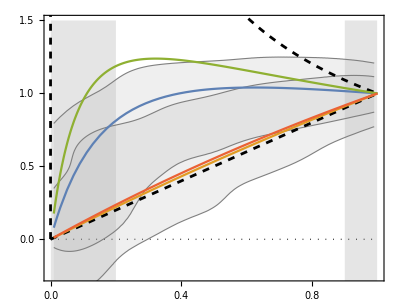

```mathematica
Show[plotNFWGrayRed, Plot[{δVnfw[rn, rsnUpper @ 1], δVnfw[rn, rsnLower @ 1] ,δVnfw[rn, 0.148732], δVnfw[rn, 5.75316]}, {rn,0.01,1}, PlotRange->All]]
```

Conclusion: the distribution of individual fits and the NAV-inferred parameters are only lightly connected. It is possible to use one to infer the other, but only as a rough approximation.

## IV. DC 14

```mathematica
Clear[X, ρ, α,γ,β]
α = 2.94 - Log10[(10^(X + 2.33))^-1.08 + (10^(X + 2.33))^2.29];
β = 4.23 + 1.34 X + 0.26 X^2;
γ = - 0.06 + Log10[(10^(X + 2.56))^-0.68 + (10^(X+2.56))];
ρDC14[rn_, rsn_, ρs_, X_] = ρs/((rn/rsn)^γ(1+ (rn/rsn)^α)^((β-γ)/α));
```

```mathematica
X100min = -410;
X100max = -130;
Xmin = X100min/100.;
Xmax = X100max/100.;

(*Clear[MDC14aux]; *) (*Uncomment this to recompute and export MDC14aux.*)
If[DownValues@MDC14aux === {}, 
  SetSharedFunction[MDC14aux];
  ParallelTable[
    MDC14aux[rn_, rsn_, ρs_, X100] = 4 π Rmax^3 Integrate[
      ρDC14[rnprime, rsn, ρs, X100 / 100] rnprime^2, {rnprime, 0, rn}, 
      Assumptions -> {rn > 0, rsn > 0}
    ], 
    {X100, X100min, X100max, 1}
  ];
  DumpSave["../MDC14aux.mx", MDC14aux]
];
```

```mathematica
Clear[MDC14, VVDC14, δVDC14];

iRound[x_] = IntegerPart[Round[x, 0.01] 100];

MDC14[rn_, rsn_, ρs_, X_] := MDC14aux[rn, rsn, ρs, iRound[X]];

VVDC14[rn_, rsn_, ρs_, X_] := G/(rn Rmax) MDC14[rn, rsn, ρs, X] ;

δVDC14[rn_, rsn_, X_] := δVDC14[rn, rsn, X] = Simplify[
  VVDC14[rn, rsn, ρs, X]/VVDC14[1, rsn, ρs, X],
  Assumptions -> {0 <= rn <= 1,  rsn > 0, Rmax > 0}
];
```

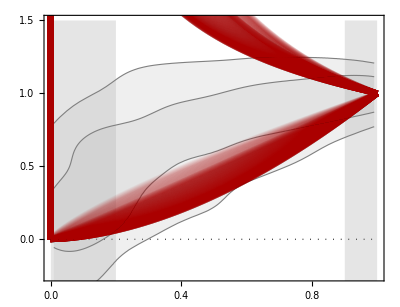

```mathematica
plotDC14GrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        Table[δVDC14[rn,1000,X], {X, Xmin, Xmax, 0.01}], 
        Table[δVDC14[rn,0.001,X], {X, Xmin, Xmax, 0.01}]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Opacity[0.05], Thickness[0.01], Darker[Red]}}
    ]
  }
]
```

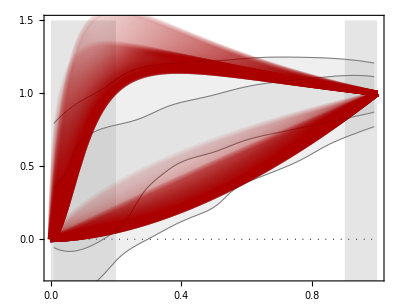

```mathematica
plotDC14GrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        Table[δVDC14[rn,10,X], {X, Xmin, Xmax, 0.01}], 
        Table[δVDC14[rn,0.1,X], {X, Xmin, Xmax, 0.01}]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Opacity[0.05], Thickness[0.01], Darker[Red]}}
    ]
  }
]
```

These definitions below are important if the NFW and Burkert sections were not run

```mathematica
plotNFWGrayRed = -Graphics-;
plotBurkertGrayRed=-Graphics-;
```

```mathematica
σSilverman = 0.082; (*The vertical KDE "error". This value will not be crucial here, since it is constant.*)

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, X_, nσ_]:= chi2Upper[rsn, X, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVDC14[rn, rsn, X])^2/ ( 2 σSilverman^2) ,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, X_, nσ_] := chi2Lower[rsn, X, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVDC14[rn,rsn, X])^2/ ( 2 σSilverman^2) , 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnUpper[1] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[2] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[1] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, X} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, X} 2σ bounds: "];
```

{rsn, X} 1σ bounds:   {{0.205538,-1.78988},{2.69658,-1.54568}}

{rsn, X} 2σ bounds:   {{0.139313,-3.88306},{50.,-2.66053}}

```mathematica
σSilverman = 0.082; (*The vertical KDE "error". This value will not be crucial here, since it is constant.*)

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, X_, nσ_]:= chi2Upper[rsn, X, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVDC14[rn, rsn, X])^2/ ( 2 σSilverman^2) ,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, X_, nσ_] := chi2Lower[rsn, X, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVDC14[rn,rsn, X])^2/ ( 2 σSilverman^2) , 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnUpper[1] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[2] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[1] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, X} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, X} 2σ bounds: "];
```

Performing the optimization.

{rsn, X} 1σ bounds:   {{0.205538,-1.78988},{2.69658,-1.54568}}

{rsn, X} 2σ bounds:   {{0.139313,-3.88306},{50.,-2.66053}}

Performing the optimization.

{rsn, X} 1σ bounds:   {{0.205538,-1.78988},{2.69658,-1.54568}}

{rsn, X} 2σ bounds:   {{0.139313,-3.88306},{50.,-2.66053}}

```mathematica
NMinimize[{chi2Lower[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}]
```

{0.20025,{rsn→2.69658,X→-1.54568}}

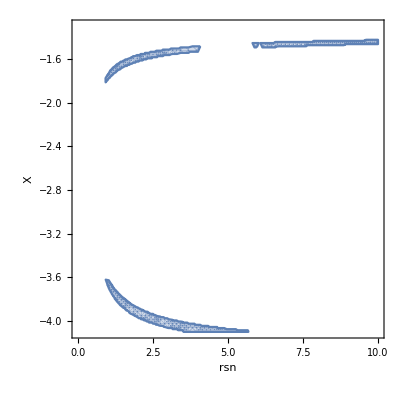

```mathematica
RegionPlot[chi2Lower[rsn, X, 1] < 0.21, {rsn, 0.01, 10}, {X, Xmin, Xmax}, MaxRecursion->4, PlotPoints->20, FrameLabel->Automatic]
```

The above plot shows that there is a strong degeneracy for DC14, at least considering the lower 1σ limiting curve. Hence, the DC14 limiting curves parameter values should be seen as examples that lead to curves that best approximate the observational limits.

plotDC14GlobalBestFit:

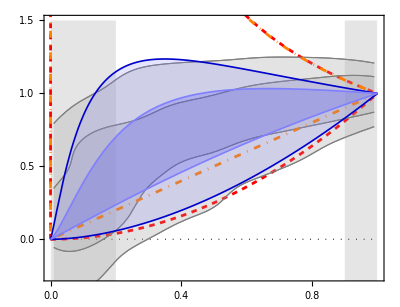

```mathematica
plotDC14GlobalBestFit = Show[
  {
    plotBurkertGrayRed /. {Dashed -> Dashing[.01], Black -> Red},
    plotNFWGrayRed /. {Dashed-> DotDashed, Black -> Orange},
    Plot[
      {
        δVDC14[rn, Sequence@@ rsnUpperR @ 2],
        δVDC14[rn, Sequence@@ rsnUpperR @ 1],
        δVDC14[rn, Sequence@@ rsnLowerR @ 2],
        δVDC14[rn, Sequence@@ rsnLowerR @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotDC14GlobalBestFit:"];
Print@plotDC14GlobalBestFit;

Export["plotDC14GlobalBestFit.pdf", plotDC14GlobalBestFit];
```

The limiting cases above show the burkert (red dashed) and NFW (orange dot-dashed) limits. They coincide in the limit of small r_s or r_c.

The DC14 profile has a clear advantage over the NFW one considering the lower 2σ bound.

## V. Partially screened gravitational potential: NFW

### V.1 Screened potential limiting cases from NFW

Using rsn for the normalized rs: rs/Rmax and rn for the normalized radius: r/Rmax, the mass and the additional normalized velocity can be them easily computed:

Since

The additional effective mass is given by

γ r^2  m''(r)

Since the mass above will be based on the NFW halo, we call the above MSaddnfw

```mathematica
ρnfw[rn_, rsn_, ρs_] = ρs/(rn/rsn(1+rn/rsn)^2);

Mnfw[rn_, rsn_, ρs_] = 4 π Rmax^3 Integrate[ρnfw[rnprime, rsn, ρs] rnprime^2, {rnprime, 0, rn}, Assumptions-> {rn>0, rsn>0}];

MSaddnfw[rn_, rsn_, ρs_] = rn^2 D[D[Mnfw[rn, rsn, ρs], rn], rn]; (* the effective additional mass*)

MSnfw[rn_, rsn_, ρs_, γ_] = Mnfw[rn, rsn, ρs] + γ MSaddnfw[rn, rsn, ρs]; (*The total effective halo mass*)

VVSnfw[rn_, rsn_, ρs_, γ_] = G/Rmax MSnfw[rn, rsn, ρs, γ]/rn;

δVSnfw[rn_, rsn_, γ_] = FullSimplify[
  VVSnfw[rn, rsn, ρs, γ] / VVSnfw[1, rsn, ρs, γ],
  Assumptions -> {0 < rn < 1, 0 < rsn < 1, 0 < Rmax}
];
```

For rsn → ∞ or rsn → 0, δVSnfw is independent from γ, and hence it has the same result of NFW.

```mathematica
Limit[δVSnfw[rn, rsn,γ] - δVSnfw[rn, rsn,0], rsn -> ∞]
Limit[δVSnfw[rn, rsn,γ] - δVSnfw[rn, rsn,0], rsn -> 0]
```

0

0

But there is an exception: when γ=-1/2 , which is a  singular value at rsn -> ∞

```mathematica
Limit[δVSnfw[rn, rsn,-1/2] - δVSnfw[rn, rsn,0], rsn -> ∞]
Limit[δVSnfw[rn, rsn,-1/2] - δVSnfw[rn, rsn,0], rsn -> 0]
```

(-1+rn) rn

0

```mathematica
δVSnfw[rn, rsn,γ]
```

((1+rsn)^3 (rn ((rn+rsn)^2+rn (rn-rsn) γ)+(rn+rsn)^3 Log[rsn/(rn+rsn)]))/(rn (rn+rsn)^3 (1+rsn (2+rsn-γ)+γ-2 (1+rsn)^3 ArcCoth[1+2 rsn]))

The expression above in general has a singularity that depends on rsn and γ.

The value of γ with a singularity is given by

```mathematica
γsing = γ /. Solve[(1+rsn (2+rsn-γ)+γ-2 (1+rsn)^3 ArcCoth[1+2 rsn]) == 0, γ] // First
```

(-1-2 rsn-rsn^2+2 (1+rsn)^3 ArcCoth[1+2 rsn])/(1-rsn)

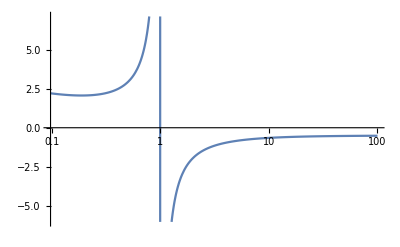

```mathematica
LogLinearPlot[γsing, {rsn, 0, 100}]
```

We intend to find now a range on the values of γ such that no singularity exists, for any rsn value.

```mathematica
FindMinimum[{γsing , 0<rsn<1}, rsn]
Quiet@Maximize[{γsing , rsn>1}, rsn]
```

{2.06866,{rsn→0.188448}}

{-1/2,{rsn→∞}}

For rsn < 1, the values of γ that make the additional contribution to diverge are positive and larger than 2 (larger than 2.069)
For rsn =1, there is no singularity.
For rsn> 1, the values of γ that make the additional contribution to diverse are negative and smaller than - 1/2.

Hence, in the range  -1/2 <  γ < 2 there is no singularity for any rsn value.

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]

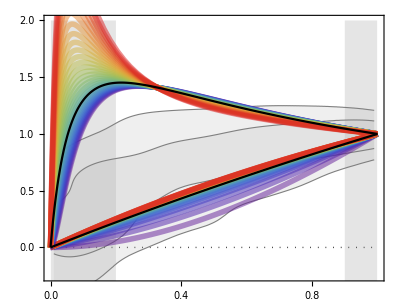

```mathematica
γmin = -0.5;
γmax = 1; (*I could have used γmax = 2, but it gets far away from the observational data*)

nγ = (γmax - γmin)/0.05 + 1;

plotSNFWGrayRed = Show[
  {
    plotBackground[2.0],
    plotSigmaRegionsRAR,
    Plot[
      {
        Evaluate@Table[δVSnfw[rn, 10, X], {X, γmin, γmax, 0.05}], 
        Evaluate@Table[δVSnfw[rn, 0.1, X], {X, γmin, γmax, 0.05}],
        δVSnfw[rn, 0.1, 0],
        δVSnfw[rn, 10, 0]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {Sequence@@Table[{Opacity[0.5], Thickness[0.01], ColorData["Rainbow"][i/nγ]}, {i, nγ}], Sequence@@Table[{Opacity[0.5], Thickness[0.01], ColorData["Rainbow"][i/nγ]}, {i, nγ}], {Black}, {Black}}
    ]
  }
]
```

### V.2. Screened NFW: Highest Density Regions for variable γ

I want to find the values of rsn that best describe the n-sigma regions.

```mathematica
plotNFWGrayRed = -Graphics-;
plotBurkertGrayRed=-Graphics-;
```

```mathematica
σSilverman = 0.082; (*The vertical KDE "error". This value will not be crucial here, since it is constant.*)

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, γ_, nσ_]:= chi2Upper[rsn, γ, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVSnfw[rn, rsn, γ])^2/ σSilverman^2 ,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, γ_, nσ_] := chi2Lower[rsn, γ, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVSnfw[rn,rsn, γ])^2/  σSilverman^2 , 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, γ} /. NMinimize[{chi2Upper[rsn, γ, 2], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];
rsnUpper[1] :=  {rsn, γ} /. NMinimize[{chi2Upper[rsn, γ, 1], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];
rsnLower[2] :=  {rsn, γ} /. NMinimize[{chi2Lower[rsn, γ, 2], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];
rsnLower[1] :=  {rsn, γ} /. NMinimize[{chi2Lower[rsn, γ, 1], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, γ} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, γ} 2σ bounds: "];
```

Performing the optimization.

{rsn, γ} 1σ bounds:   {{1.31022,1.},{6.46224,0.0888792}}

{rsn, γ} 2σ bounds:   {{0.136188,-0.5},{50.,-0.5}}

plotSnfwGlobalBestFit:

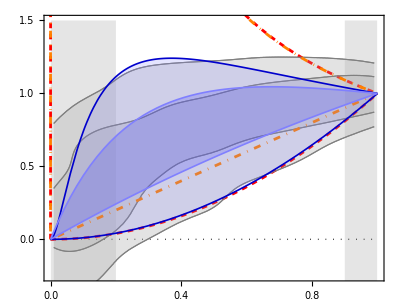

```mathematica
plotSnfwGlobalBestFit = Show[
  {
    plotBurkertGrayRed /. {Dashed -> Dashing[.01], Black -> Red},
    plotNFWGrayRed /. {Dashed -> DotDashed, Black -> Orange},
    Plot[
      {
        δVSnfw[rn, Sequence@@ rsnUpperR @ 2],
        δVSnfw[rn, Sequence@@ rsnUpperR @ 1],
        δVSnfw[rn, Sequence@@ rsnLowerR @ 2],
        δVSnfw[rn, Sequence@@ rsnLowerR @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotSnfwGlobalBestFit:"];
Print@plotSnfwGlobalBestFit;

Export["plotSnfwGlobalBestFit.pdf", plotSnfwGlobalBestFit];
```

### V.3 - Efficiency for variable γ

```mathematica
e1 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 1)] &, δVSnfw[#, Sequence@@(rsnUpper@ 1)] &, 1]
```

{0.787995,0.862174,0.0741791}

```mathematica
e2 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 2)] &, δVSnfw[#, Sequence@@(rsnUpper@ 2)] &, 2]
```

{0.856881,0.872317,0.015436}

```mathematica
(e1 + e2)/2
```

{0.822438,0.867246,0.0448076}

### V.4. Screened NFW: Highest Density Regions for CONSTANT γ

```mathematica
Clear[rsnγUpper,rsnγLower];
rsnγUpper[n_, γ_] :=  {γ, NMinimize[{chi2Upper[rsn, γ, n], 50>rsn>0.1}, rsn]};
rsnγLower[n_, γ_] :=  {γ, NMinimize[{chi2Lower[rsn, γ, n], 50>rsn>0.1}, rsn]};
```

```mathematica
tab = ParallelTable[{γ, Sum[rsnγUpper[n, γ][[2,1]] + rsnγLower[n, γ][[2,1]], {n,1,2}]}, {γ, -0.5, 1, 0.01}];
```

```mathematica
Sort[tab, #1[[2]]<#2[[2]]&]
```

{{-0.5,2.13253},{-0.49,2.60637},{-0.48,2.93568},{-0.47,3.23133},{-0.46,3.50811},{-0.45,3.77376},{-0.44,4.03018},{-0.43,4.27909},{-0.42,4.52261},{-0.41,4.75938},{-0.4,4.99084},{-0.39,5.21729},{-0.38,5.43885},{-0.37,5.65557},{-0.36,5.86744},{-0.35,6.07435},{-0.34,6.27616},{-0.33,6.47264},{-0.32,6.66353},{-0.31,6.84849},{-0.3,7.02716},{-0.29,7.19908},{-0.28,7.36375},{-0.27,7.52059},{-0.26,7.66896},{-0.25,7.80811},{-0.24,7.93721},{-0.23,8.05533},{-0.22,8.1612},{-0.21,8.25382},{-0.2,8.33197},{-0.19,8.39406},{-0.18,8.43826},{-0.17,8.46966},{-0.16,8.49977},{-0.15,8.5288},{-0.14,8.55703},{-0.13,8.58408},{-0.12,8.6103},{-0.11,8.63578},{-0.1,8.66056},{-0.09,8.68587},{-0.08,8.70949},{-0.07,8.73166},{-0.06,8.7543},{-0.05,8.77653},{-0.04,8.79837},{-0.03,8.81986},{-0.02,8.84104},{1.,8.84752},{0.99,8.85762},{-0.01,8.86194},{0.98,8.8681},{0.97,8.87898},{0.,8.88258},{0.96,8.89028},{0.95,8.90201},{0.01,8.90299},{0.94,8.91418},{0.02,8.92319},{0.93,8.92681},{0.92,8.93992},{0.03,8.94281},{0.91,8.95353},{0.04,8.96304},{0.9,8.96764},{0.05,8.98169},{0.89,8.98227},{0.88,8.99745},{0.06,9.00103},{0.87,9.01318},{0.07,9.02029},{0.86,9.02948},{0.08,9.0395},{0.85,9.04732},{0.09,9.05864},{0.84,9.0648},{0.1,9.07773},{0.83,9.08176},{0.11,9.09676},{0.82,9.10046},{0.12,9.11572},{0.81,9.11976},{0.13,9.13458},{0.8,9.13971},{0.14,9.15337},{0.79,9.16028},{0.15,9.17208},{0.78,9.18148},{0.16,9.19071},{0.77,9.20331},{0.17,9.20924},{0.76,9.22573},{0.18,9.22767},{0.19,9.24707},{0.75,9.24875},{0.2,9.26418},{0.74,9.27233},{0.21,9.28324},{0.73,9.29644},{0.22,9.30014},{0.23,9.3179},{0.72,9.32104},{0.24,9.33549},{0.71,9.34607},{0.25,9.35292},{0.26,9.37018},{0.7,9.37147},{0.27,9.38726},{0.69,9.39729},{0.28,9.40418},{0.29,9.42092},{0.68,9.42318},{0.3,9.4375},{0.67,9.44916},{0.31,9.45392},{0.32,9.47016},{0.66,9.4751},{0.33,9.48624},{0.65,9.50086},{0.34,9.50218},{0.35,9.518},{0.64,9.52625},{0.36,9.53483},{0.37,9.54928},{0.63,9.55111},{0.38,9.56551},{0.62,9.57522},{0.39,9.58058},{0.4,9.59544},{0.61,9.59833},{0.41,9.61006},{0.6,9.62018},{0.42,9.62438},{0.43,9.63833},{0.59,9.64049},{0.44,9.6518},{0.58,9.65898},{0.45,9.66466},{0.57,9.67532},{0.46,9.67672},{0.47,9.68774},{0.56,9.68922},{0.48,9.69745},{0.55,9.70042},{0.49,9.70551},{0.54,9.70868},{0.5,9.71152},{0.53,9.71388},{0.51,9.71513},{0.52,9.71599}}

So the best gamma is γ = - 0.5. Note that this γ value only has a singularity at rsn -> ∞. Lower values of γ have singularity at finite rsn values.

plotSNFWglobalGammaGrayRed:

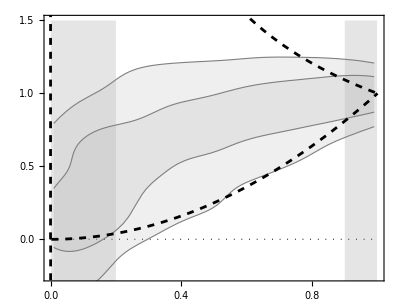

```mathematica
γbest = -0.5;

plotSNFWglobalGammaGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVSnfw[rn, 1000, γbest], 
        δVSnfw[rn, 0.001, γbest]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotSNFWglobalGammaGrayRed:"];
Print@plotSNFWglobalGammaGrayRed;
```

I want to find the values of rsn that best describe the n-sigma regions.

Performing the optimization.

rsn 1σ bounds:   {0.206369,0.986519}

rsn 2σ bounds:   {0.119189,2606.74}

plotNFWGlobalGammaBestFit:

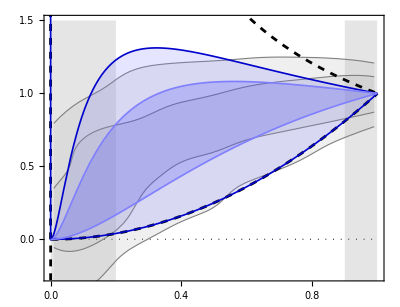

```mathematica
(* SPECIFIC DEFINITIONS *)

rnStart = 0.01;
rnEnd=0.99;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rsnUpper[2] = rsn /. NMinimize[{chi2Upper[rsn, γbest, 2], rsn > 0}, {rsn, 0, 1}][[2]];
rsnUpper[1] = rsn /. NMinimize[{chi2Upper[rsn, γbest, 1], rsn > 0}, {rsn, 0, 1}][[2]];
rsnLower[2] = rsn /. NMinimize[{chi2Lower[rsn, γbest, 2], rsn > 0}, {rsn, 10, 1000}][[2]];
rsnLower[1] = rsn /. NMinimize[{chi2Lower[rsn, γbest, 1], rsn > 0}, {rsn, 10, 1000}][[2]];

Echo[{rsnUpper[1], rsnLower[1]}, "rsn 1σ bounds: "];
Echo[{rsnUpper[2], rsnLower[2]}, "rsn 2σ bounds: "];

plotNFWGlobalGammaBestFit = Show[
  {
    plotSNFWglobalGammaGrayRed,
    Plot[
      {
        δVSnfw[rn, rsnUpper @ 2, γbest],
        δVSnfw[rn, rsnUpper @ 1, γbest],
        δVSnfw[rn, rsnLower @ 2, γbest],
        δVSnfw[rn, rsnLower @ 1, γbest]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotNFWGlobalGammaBestFit:"];
Print@plotNFWGlobalGammaBestFit;

Export["plotNFWGlobalGammaBestFit.pdf", plotNFWGlobalGammaBestFit];
```

### V.5 - Efficiency for CONSTANT γ

```mathematica
rsnLower@ 1
```

0.986519

```mathematica
Sequence@@(rsnLower@ 1)
```

0.986519

```mathematica
e1 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 1), γbest] &, δVSnfw[#, Sequence@@(rsnUpper@ 1), γbest] &, 1]
```

{0.689171,0.886622,0.197451}

```mathematica
e2 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 2), γbest] &, δVSnfw[#, Sequence@@(rsnUpper@ 2), γbest] &, 2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.836023,0.887752,0.0517292}

```mathematica
(e1 + e2)/2
```

{0.762597,0.887187,0.12459}

This efficiency is a bit better than the Burkert efficiency!

## VI. Exponential profiles for stars and gas: Necessary for modified gravity applications

## III.1. Stellar contribution

```mathematica
Clear[vExp, fitExpVdisk, fitExpVdiskPlot, chi2, associationFitExpVdisk];

(*vExp comes from Binney & Tremaine 2nd Ed., eq.(2.165)*)
vExp[R_,logSigma0_,h_]= Block[{y}, 
  y = R/(2 h);
  kpc Sqrt[4 π G0 10^logSigma0 h y^2 (BesselI[0,y] BesselK[0,y] - BesselI[1,y] BesselK[1,y])]
];

chi2[model_List, dataObs_List, uncertainty_List] := chi2[model, dataObs, uncertainty]  = Total[(model-dataObs)^2/uncertainty^2];

associationFitExpVdisk::usage="associationFitExpVdisk[data(R x Vdisk)] fits the radial vs disk velocity curve data as a rotation curve for an exponential disk and returns an association with several data. "<>
  "For fitting, it is assumed an uncertainty of 10% on the velocity. The important point is not the porportionality constant, but that the uncertainty is proportional to the velocity. "<>
  "If data = {},  associationFitExpVdisk returns {}.";

associationFitExpVdisk[dataRVdisk_List] := fitExpVdisk[dataRVdisk] = Block[
  {sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  rMax = Last @ dataRVdisk[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVdisk[[All,1]];
  uncertainty = Max[{0.10 dataRVdisk[[#, 2]], 2}] & /@ Range@Length@dataRVdisk; (*Assumes uncertainty of 10% or 2 km/s. *)
  sol = NMinimize[
    {chi2[listModel, dataRVdisk[[All, 2]], uncertainty], h > 0, logSigma0 > 1},
    {{logSigma0, 6, 10}, {h, 0.5, 10}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {First@sol, First@sol/(Length[dataRVdisk] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVdisk]} /. Last@sol;
  AssociationThread[{"Chi2", "Chi2red", "logSigma0", "h", "hn", "rMax", "dataPoints"}, solExtended]
];

plotFittedExpVdisk[dataRVdisk_List, bestVdiskValues_List]:= Block[
  {vMax, bestLogSigma0, besth, rMax},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  {bestLogSigma0, besth} = bestVdiskValues;
  vMax = Max @ dataRVdisk[[All, 2]];
  rMax = Last @ dataRVdisk[[All, 1]];
  Show[
    {
      ListPlot[
        dataRVdisk,
        PlotRange -> {{0, 1.1 * rMax}, {0, 1.1 * vMax}}
      ],
      Plot[vExp[R, bestLogSigma0, besth], {R, 0, 100}, PlotRange -> All]
    }
  ]
];
```

```mathematica
Echo["Computing datasetExpVdiskNoBulge. This takes some seconds."];
datasetExpVdiskNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVdisk[gdRBulgeless[{Rad, Vdisk}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVdiskNoBulge. This takes some seconds.

40.0019

```mathematica
Export["headerAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# The complete Table B1 data: the best fit results of an exponential model for the stellar component of 122 SPARC galaxies.",
  "# First column: best-fit disk scale length (h).",
  "# Second column: best-fit central surface brightness (logSigma0).",
  "# Third column: normalized disk scale length (hn).",
  "# Fourth column: the minimum chi-squared value (Chi2).",
  "# Fifth column: the number of galaxy data points that were used for the fit (dataPoints).", 
  "# ",
  "# "
}];

datasetStarsExport = datasetExpVdiskNoBulge[All,{"h","logSigma0", "hn","Chi2", "dataPoints"}];
Export["StellarExponentialBestFitAux.tsv", datasetStarsExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerAux.txt StellarExponentialBestFitAux.tsv > StellarExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerAux.txt"];
DeleteFile["StellarExponentialBestFitAux.tsv"];
```

### III.1.1. The hn distribution

1σ limits:  {0.0629196,0.293442}

2σ limits:  {0.0299119,0.474179}

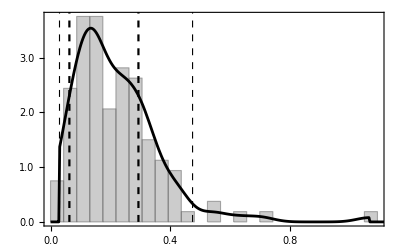

```mathematica
listhn= Normal @ datasetExpVdiskNoBulge[All, "hn"];

dist = SmoothKernelDistribution[
  listhn,
  silvermanBw @ listhn,
  MaxExtraBandwidths -> 0,
  InterpolationPoints -> 10^4 (*This is a large number, it has no relevant impact on speed *)
];

listHDPDFlimits = FindHDPDFValues[dist, oneAndTwoSigma];

list2PointsXPDF = {dist["InterpolationPoints"], dist["PDFValues"]}ᵀ;
positionMaxPDF = First @ Last @ SortBy[list2PointsXPDF, Last];

rootsSigma[i_] := (FindRoot[
  PDF[dist, x] == listHDPDFlimits[[i]], 
  #, 
  MaxIterations -> 1000
] & /@ {{x, 0, positionMaxPDF}, {x, positionMaxPDF, 1}}) ~ Quiet ~ FindRoot::brmp;

{hnLow[1], hnHigh @ 1} = x /. rootsSigma[1];
{hnLow[2], hnHigh @ 2} = x /. rootsSigma[2];

Clear @ lines;
lines[nSigmas_] := {
  Dashed,
  Thickness[0.004 / nSigmas],
  Line @ {{hnLow @ nSigmas, 0}, {hnLow @ nSigmas, 100}},
  Line @ {{hnHigh @ nSigmas, 0}, {hnHigh @ nSigmas, 100}}
};

Echo[{hnLow @ 1, hnHigh @ 1} ,"1σ limits:"];
Echo[{hnLow @ 2, hnHigh @ 2} ,"2σ limits:"];

Show[
  {
    Histogram[listhn,
      {silvermanBw @ listhn},
      "PDF", histoOptions, Epilog -> {lines @ 1, lines @ 2},
      PlotRange -> All
    ],
    nPlot[PDF[dist, x], {x, 0, 10}]
  }
]
```

### III.1.2. Deriving the hGasn, frho and fh values for each galaxy

hGas is the h value for the gas distribution.
hGasn is the hn value for the gas distribution.
frho is the ratio between the gas to stellar central density.
fh is the ratio between hn and hGasn.

#### logSigma0gas e hGasn

```mathematica
Clear[associationFitExpVgas];
associationFitExpVgas[dataRVgas_List] := associationFitExpVgas[dataRVgas] = Block[
  {sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVgas=={}, 
    Return[{}]
  ];
  rMax = Last @ dataRVgas[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVgas[[All,1]];
  uncertainty = Max[{0.10 dataRVgas[[#, 2]], 2}] & /@ Range@Length@dataRVgas; (*Max[10%, 2 km/s] uncertainty, inspired on distance error together with a minimum one.*)
  sol = NMinimize[
    {chi2[listModel, dataRVgas[[All, 2]], uncertainty], 100 rMax > h > 0.1, logSigma0 > 0.5},
    {{logSigma0, 3, 10}, {h, 3, 30}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {First@sol, First@sol/(Length[dataRVgas] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVgas]} /. Last@sol;
  AssociationThread[{"Chi2", "Chi2red", "logSigma0Gas", "hGas", "hGasn", "rMax", "dataPoints"}, solExtended]
];
```

```mathematica
Echo["Computing datasetExpVgasNoBulge. This takes some seconds."];
datasetExpVgasNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVgas[gdRBulgeless[{Rad, Vgas}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVgasNoBulge. This takes some seconds.

50.9186

```mathematica
Export["headerGasAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# This file: Best fit results of an exponential model for the gaseous component of 122 SPARC galaxies.",
  "# First column: best-fit disk scale length (hGas).",
  "# Second column: best-fit central surface brightness (logSigma0Gas).",
  "# Third column: normalized disk scale length (hGasn).",
  "# Fourth column: the minimum chi-squared value (Chi2).",
  "# Fifth column: the number of galaxy data points that were used for the fit (dataPoints).", 
  "# ",
  "# "
}];

datasetGasExport = datasetExpVgasNoBulge[All,{"hGas","logSigma0Gas", "hGasn","Chi2", "dataPoints"}];
Export["GasExponentialBestFitAux.tsv", datasetGasExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerGasAux.txt GasExponentialBestFitAux.tsv > GasExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerGasAux.txt"];
DeleteFile["GasExponentialBestFitAux.tsv"];
```

#### frho, fh and hn vectors

```mathematica
list1hn = Normal@datasetExpVdiskNoBulge[All, "hn"];
list1hGasn = Normal@datasetExpVgasNoBulge[All, "hGasn"];
list1logSigma0 = Normal@datasetExpVdiskNoBulge[All, "logSigma0"];
list1logSigmaGas0 = Normal@datasetExpVgasNoBulge[All, "logSigma0Gas"];

list1frho = list1logSigmaGas0/ (0.5 list1logSigma0) (*The 0.5 comes from the mass to light ratio*);
list1fh = list1hn/ list1hGasn;
```

## VII. Palatini

## IV.1. Additional contribution from stars only (to warm up)

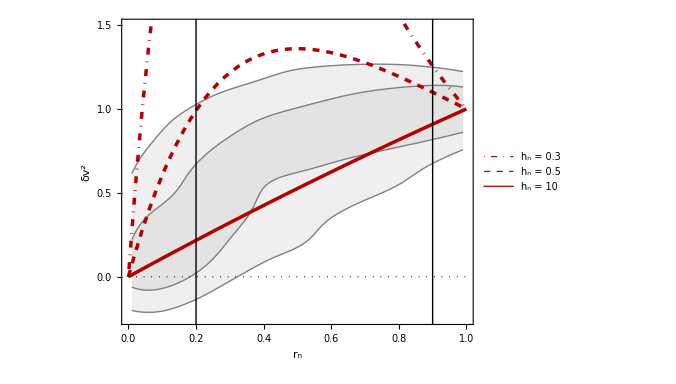

```mathematica
δvP2[rn_, hn_] = rn Exp[(1-rn) / hn];

plot100 := nPlot[
  100,
  {rn, 0, 1},
  PlotRange -> {{0, 1}, {-0.25, 1.5}},
  AspectRatio -> (1 / 1.3),
  GridLines -> None, 
  ImageSize -> 500, 
  FrameStyle -> 18, 
  Epilog -> 
  {
    Line[{{0.2, -0.5}, {0.2, 2}}],
    Line @ {{0.9, -0.5}, {0.9, 2}},
    Dotted,
    Line @ {{0, 0}, {1, 0}}
  }
];

plotPalatiniStars := Plot[
  {δvP2[rn, 0.3], δvP2[rn, 0.5], δvP2[rn, 10]},
  {rn, 0, 1},
  PlotRange -> All,
  PlotStyle -> 
  {
    {Thickness[0.005], DotDashed, Darker[Red, 0.3]},
    {Thickness[0.005], Dashed, Darker[Red, 0.3]},
    {Thickness[0.005], Darker[Red, 0.3]}
  },
  PlotLegends->Placed[
    {
      Style["h_n = 0.3",17, FontFamily->Times], 
      Style["h_n = 0.5",17, FontFamily->Times], 
      Style["h_n = 10",17, FontFamily->Times]
    },
    {{0.76,0.26},{0.5,0.5}}
  ]
];

Show[{plot100, plotSigmaRegionsRARNoBulge, plotPalatiniStars}, 
  FrameLabel->{Style["r_n", 20, FontFamily->Times], Style["δv^2", 20, FontFamily->Times]}
]
```

Conclusions: there is a significant  region that cannot covered by this Palatini case. 
The curve for hn=10 is essentially the same for any curve with hn > 10: a straightline.
Also, the necessary hn values to cover  the most dense regions are unrealistic, as detailed below.

## IV.2. Stars and Gas for Palatini

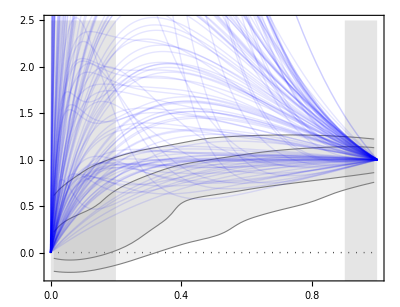

```mathematica
δvP2g[rn_, hn_, fh_, frho_]= (rn ( ⅇ^(-rn/hn)+  frho  fh ⅇ^(- fh rn/hn)))/( ⅇ^(-1/hn)+  frho fh  ⅇ^(- fh /hn));
δvPalatini[rn_, gal_] := δvP2g[rn, list1hn[[gal]], list1fh[[gal]], list1frho[[gal]]];
Show[plotBackground[2.5],
  plotSigmaRegionsRARNoBulge,
  Plot[Evaluate[δvPalatini[rn, #] & /@ Range@122], {rn, 0, 1}, 
PlotRange -> All, 
PlotStyle-> Directive[Opacity[0.1],Blue, Thick]]
]
```

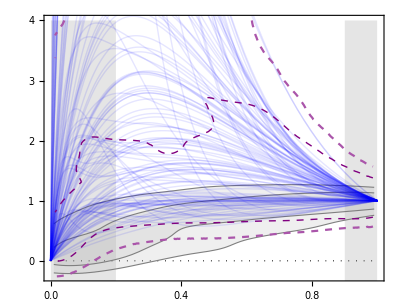

```mathematica
Clear @ list2δVVmodel;
list2δVVmodel[gal_] := Table[{rn, δvPalatini[rn, gal]}, {rn, RandomReal[1,200]}];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ 122, {}], 1];

distPalatini = distributionSilverman @ list2δVVmodelAll;
list1LimitsSigmaPalatini = FindHDPDFValues[distPalatini, oneAndTwoSigma];
(*plotBluePalatini = plotBlue[list2δVVmodelAll, list1LimitsSigmaPalatini, {{xmin, xmax - 0.01}, {-0.5, 2.5}}, PlotRange -> {{0, 0.99}, {-0.5, 2.5}}] *)

plotPalatiniCurves = Plot[Evaluate[δvPalatini[rn, #] & /@ Range@122], {rn, 0, 1}, PlotRange -> All, PlotStyle-> Directive[Opacity[0.1],Blue, Thick]];

plotPalatiniContours = ContourPlot[
  {
    PDF[distPalatini, {x,y}] == list1LimitsSigmaPalatini[[1]], 
    PDF[distPalatini, {x,y}] == list1LimitsSigmaPalatini[[2]]
  }, 
  {x,0,1}, {y,-0.5, 4.0},  
  ContourStyle -> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}];

Show[
  plotBackground[4.0],
  plotSigmaRegionsRARNoBulge,
  plotPalatiniCurves,
  plotPalatiniContours
]

Export["plotdeltaVPalatini.pdf", %];
```

## VIII. MOND

## V.1 MOND observational data without approximations (all 153 galaxies)

```mathematica
Clear[a0, aNewtList, aNewt, ΔVVmodel, rmax, interpolVbar, interpolVbarSquared, VVmodel, δVVmodel];

rmax[gal_] := Last[gdR[Rad, gal]];

aNewtList[gal_]:=Block[{vvbar, aux},
  vvbar = squareSign[gdR[Vbar, gal]];
  (*vvbar = Total[{ squareSign[#1], 0.5 squareSign[#2], 0.6 squareSign[#3] }] & @@@ gdR[{Vgas, Vdisk, Vbulge},gal];*)
  aux = {gdR[Rad,gal], vvbar/(kpc gdR[Rad,gal])}ᵀ;
  Prepend[aux, {0,0}]
];

aNewt[R_, gal_] := aNewt[R, gal] = Interpolation[aNewtList[gal], Method->"Spline", InterpolationOrder->2][R];

VVmodel[R_, gal_] := R kpc aNewt[R, gal]/(1 - ⅇ^(-√(RealAbs[aNewt[R, gal]]/a0)));

ΔVVmodel[R_, gal_] := VVmodel[R, gal] - aNewt[R, gal] R kpc ;

δVVmodel[rn_, gal_] := If[gdR[Rad, gal]=={}, 
  {}, 
  ΔVVmodel[rn rmax[gal], gal] / ΔVVmodel[rmax[gal], gal]
];
```

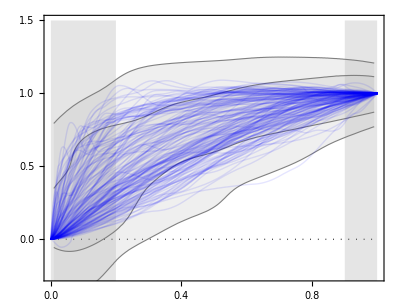

```mathematica
a0 = 1;
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  Plot[
    Evaluate[δVVmodel[rn, #]& /@ Range@175], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All
  ]
]

Export["plotdeltaVmonda01.pdf", %];
```

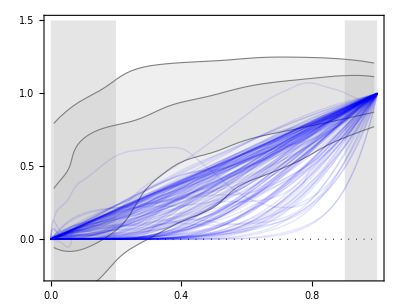

```mathematica
a0 = 10^-15;
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  Plot[
    Evaluate[δVVmodel[rn, #]& /@ Range@175], {rn,0,1},  
    PlotStyle -> Directive[Opacity[0.1], Blue, Thick], PlotRange -> All
  ]
]

Export["plotdeltaVmonda015.pdf", %];
```

The galaxy with a bump above 1 has the number 114. It has an unnusual feature: at about rn = 0.8 it has a local minimum in its acceleration. Hence, this oscilation above is not a numerical error, it reflects a property of this galaxy.

#### Comparison of the MOND distribution with the SPARC δv^2 distribution

```mathematica
a0 = 1.2 10^-13;
Clear @ list2δVVmodel;
list2δVVmodel[gal_] := If[
  gdR[Rad, gal] == {},
  {},
  Table[{rn, δVVmodel[rn, gal]}, {rn, RandomReal[1,70]}]
];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ 175, {}], 1];
```

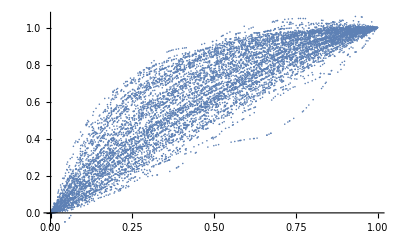

```mathematica
ListPlot @ list2δVVmodelAll
```

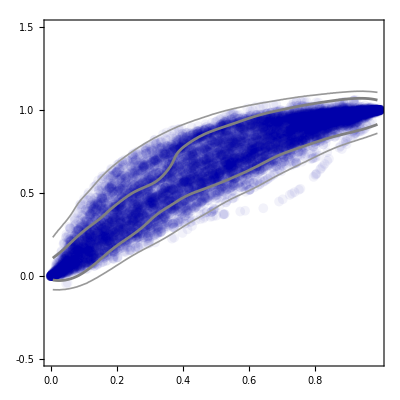

```mathematica
list1LimitsSigmaMondRaw = FindHDPDFValues[distributionSilverman @ list2δVVmodelAll, oneAndTwoSigma];
plotBlueMondRaw = plotBlue[
  list2δVVmodelAll, 
  list1LimitsSigmaMondRaw, 
  {{xmin, xmax - 0.01}, {-0.5, 1.5}}, 
  PlotRange -> {{0, 0.99}, {-0.5, 1.5}}
]
```

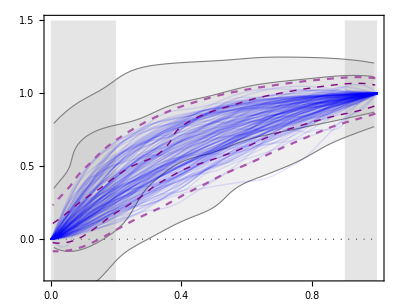

```mathematica
distMondRaw =distributionSilverman @ list2δVVmodelAll;

plotMondCurves = Plot[
  Evaluate[δVVmodel[rn, #] & /@ Range@175], {rn, 0, 1}, 
  PlotRange -> All, PlotStyle -> Directive[Opacity[0.1],Blue, Thick]
];

plotMondContours = ContourPlot[
  {
    PDF[distMondRaw, {x,y}] == list1LimitsSigmaMondRaw[[1]], 
    PDF[distMondRaw, {x,y}] == list1LimitsSigmaMondRaw[[2]]
  }, 
  {x,0,1}, {y,-0.5, 1.5},  
  ContourStyle -> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}
];

Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  plotMondCurves,
  plotMondContours
]

Export["plotdeltaVmondPrincipal.pdf", %];
```

## V.2 MOND with exponential approximations : 122 galaxies

```mathematica
Clear[a0, rn, datasetDisk, datasetGas, auxTab, list1δVVMondExp, list2δVVMondExpAux, VVbarExp, aNewtExp, VVMondExp, δVVMondExp, numberGalaxies, nG, ΔVVMondExp, rMax, dataGal];

datasetDisk = datasetExpVdiskNoBulge;
datasetGas = datasetExpVgasNoBulge;

numberGalaxies = Length @ datasetDisk;
nG = numberGalaxies; (*122 galaxies without Bulge*)

VVbarExp[R_, logSigma0_, h_, logSigmaGas0_, hgas_] := 0.5 vExp[R, logSigma0, h]^2 + vExp[R, logSigmaGas0, hgas]^2;

dataGal[gal_] := dataGal[gal] = {
  datasetDisk[gal, "logSigma0"], 
  datasetDisk[gal, "h"], 
  datasetGas[gal, "logSigma0Gas"], 
  datasetGas[gal, "hGas"]
};

rMax[gal_] := rMax[gal] = datasetDisk[gal, "rMax"];

VVbarExp[R_, gal_Integer] := VVbarExp[R, Sequence @@ dataGal[gal]];

aNewtExp[R_, gal_] :=  VVbarExp[R, gal]/ (R kpc);

VVMondExp[R_, gal_] :=  R kpc aNewtExp[R, gal]/(1 - ⅇ^(-√(aNewtExp[R, gal] / a0)));

ΔVVMondExp[R_, gal_] := VVMondExp[R, gal] - VVbarExp[R, gal];

δVVMondExpAux[rn_, gal_Integer] := ΔVVMondExp[rn rMax[gal], gal] / ΔVVMondExp[rMax[gal], gal];

(*To speed up the plots, it is relevant to define δVVMondExp from a list of interpolated functions (list1δVVMondExp)*)
list1δVVMondExp[rni_] = Block[
  {list2δVVMondExpAux},
  list2δVVMondExpAux[gali_] := Prepend[
    Table[{rni,δVVMondExpAux[rni, gali]}, {rni, 0.05, 1, 0.05}], 
    {0,0}
  ];
  Table[
    Interpolation[list2δVVMondExpAux[gali]][rni], 
  {gali, nG}
  ]
];

δVVMondExp[rn_, gal_] :=  list1δVVMondExp[rn][[gal]]
```

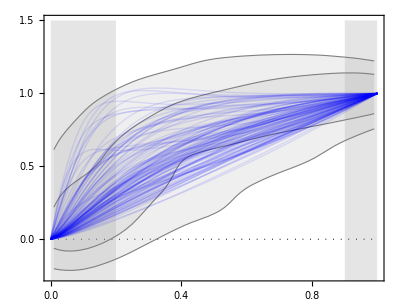

```mathematica
a0 = 1;
Show[
  plotBackground[1.5],
  plotSigmaRegionsRARNoBulge,
  Plot[
    Evaluate[δVVMondExp[rn, #]& /@ Range @ nG], {rn,0,1}, 
    PlotStyle -> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All
  ]
]

Export["plotdeltaVmondExpa01.pdf", %];
```

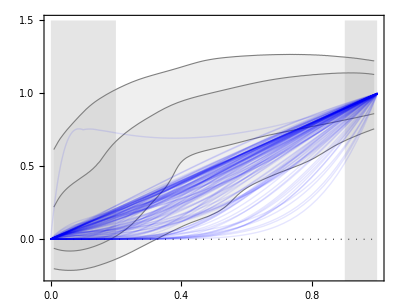

```mathematica
a0 = 10^-15;
Show[
  plotBackground[1.5],
  plotSigmaRegionsRARNoBulge,
  Plot[
    Evaluate[δVVMondExp[rn, #]& /@ Range @ nG], {rn,0,1}, 
    PlotStyle -> Directive[Opacity[0.1], Blue, Thick], PlotRange -> All
  ]
]

Export["plotdeltaVmondExpa015.pdf", %];
```

#### Comparison of the MONDExp distribution with the SPARC δv^2 distribution -- It takes minutes to run.

```mathematica
a0 = 1.2 10^-13;
Clear @ list2δVVmodel;
list2δVVmodel[gal_] := Table[{rn, δVVMondExp[rn, gal]}, {rn, RandomReal[1,70]}];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ nG, {}], 1];
distMondExp =distributionSilverman@list2δVVmodelAll;

list1LimitsSigmaMondExp = FindHDPDFValues[distMondExp, oneAndTwoSigma];
```

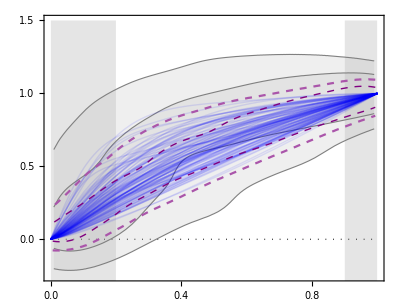

```mathematica
plotMondCurves = Plot[
  Evaluate[δVVMondExp[rn, #] & /@ Range@ nG], {rn, 0, 1}, 
  PlotRange -> All, PlotStyle -> Directive[Opacity[0.1],Blue, Thick]
];

plotMondContours = ContourPlot[
  {
    PDF[distMondExp, {x,y}] == list1LimitsSigmaMondExp[[1]], 
    PDF[distMondExp, {x,y}] == list1LimitsSigmaMondExp[[2]]
  }, 
  {x,0,1}, {y,-0.5, 1.5},  
  ContourStyle -> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}
];

Show[
  plotBackground[1.5],
  plotSigmaRegionsRARNoBulge,
  plotMondCurves,
  plotMondContours
]

Export["plotdeltaVmondExpPrincipal.pdf", %];
```

## IX. RGGR

```mathematica
(*phiDisk and phiGas come from Binney & Tremaine 2nd Ed., eq.(2.164a)*)
Clear[phiExpDisk, phiExpGal, phiExpGal, ΔVVRGGR, δVVRGGR]

phiExpDisk[R_,logSigma0_,h_] = Block[{y, logSigma0, h, R}, 
  y = R/(2 h);
  - 4 π G0 10^logSigma0 R (BesselI[0,y] BesselK[1,y] - BesselI[1,y] BesselK[0,y])
];

phiExpGal[R_, logSigma0_, h_, logSigmaGas0_, hGas_] = 0.5 phiExpDisk[R, logSigma0, h] + phiExpDisk[R, logSigmaGas0, hGas];

phiExpGal[R_, gal_Integer] := phiExpGal[R, gal] = phiExpGal[R, Sequence @@ dataGal[gal]];

ΔVVRGGR[R_, gal_] := - VVInfty VVbarExp[R, gal] / phiExpGal[R, gal];

δVVRGGRAux[rn_, gal_Integer] := δVVRGGRAux[rn, gal] =  ΔVVRGGR[rn rMax[gal], gal] / ΔVVRGGR[rMax[gal], gal];

(*To speed up the plots, it is relevant to define δVVMondExp from a list of interpolated functions (list1δVVMondExp)*)
l1δVVRGGR[rni_] = Block[
  {l2δVVRGGRAux},
  l2δVVRGGRAux[gali_] := Prepend[
    Table[{rni, δVVRGGRAux[rni, gali]}, {rni, 0.05, 1, 0.05}], 
    {0,0}
  ];
  Table[
    Interpolation[l2δVVRGGRAux[gali]][rni], 
  {gali, nG}
  ]
];

δVVRGGR[rn_, gal_] :=  l1δVVRGGR[rn][[gal]]
```

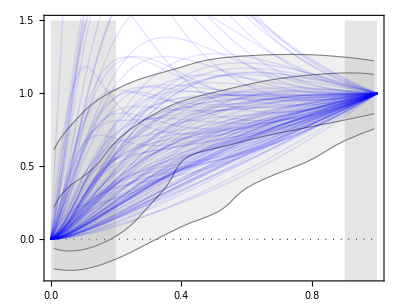

```mathematica
Show[
plotBackground[1.5],
plotSigmaRegionsRARNoBulge,
Plot[Evaluate[δVVRGGR[rn, #]& /@ Range @ nG], {rn,0,1}, PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All]]
```

```mathematica
l2δVVRGGRdiscrete[gal_] := Table[{rn, δVVRGGR[rn, gal]}, {rn, RandomReal[1,200]}];
l2δVVRGGRdiscreteAll = Flatten[l2δVVRGGRdiscrete /@ Range @ nG, 1];
distRGGR =distributionSilverman @ l2δVVRGGRdiscreteAll;

l1LimitsSigmaRGGR = FindHDPDFValues[distRGGR, oneAndTwoSigma];
```

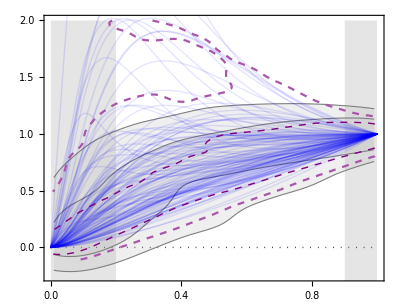

```mathematica
plotRGGRCurves = Plot[
  Evaluate[δVVRGGR[rn, #] & /@ Range@ nG], {rn, 0, 1}, 
  PlotRange -> All, PlotStyle -> Directive[Opacity[0.1],Blue, Thick]
];

plotRGGRContours = ContourPlot[
  {
    PDF[distRGGR, {x,y}] == l1LimitsSigmaRGGR[[1]], 
    PDF[distRGGR, {x,y}] == l1LimitsSigmaRGGR[[2]]
  }, 
  {x,0,1}, {y,-0.5, 2.0},  
  ContourStyle -> {Directive[Purple, Dashed, Thick], Directive[Lighter@Purple, Dashed]}
];

Show[
  plotBackground[2.0],
  plotSigmaRegionsRARNoBulge,
  plotRGGRCurves,
  plotRGGRContours
]

Export["plotdeltaVRGGR.pdf", %];
```

## X. NAV efficiency

## VII.1. NAV efficiency for region boundaries that are functions (much faster)

```mathematica
δVobs1σL[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[1]][xn]; (*L stands for lower limit*)
δVobs1σU[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[2]][xn]; (*U stands for upper limit*)
δVobs2σL[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[3]][xn];
δVobs2σU[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[4]][xn];

positivePart[x_] := HeavisideTheta[x] x;

Clear[areaObs];
areaObs[numberOfSigmas_] := Which[
  numberOfSigmas == 1, NIntegrate[δVobs1σU[xn] - δVobs1σL[xn], {xn, 0.2, 0.9}],
  numberOfSigmas == 2, NIntegrate[δVobs2σU[xn] - δVobs2σL[xn], {xn, 0.2, 0.9}],
  True, Echo["Wrong number of sigmas specification. Aborting."]; Abort[]
];
  
efficiencyNAV[ModelSigmaL_, ModelSigmaU_, numberOfSigmas_Integer] := Block[ (*There is another efficiencyNAV function with different number of arguments.*)
  {
    areaIntersection,
    areaModelOut,
    xn, (*equivalent to rn, used to avoid definition clash*)
    δVobsL,
    δVobsU
  },
  
  Which[
    numberOfSigmas == 1, δVobsL = δVobs1σL; δVobsU = δVobs1σU,
    numberOfSigmas == 2, δVobsL = δVobs2σL; δVobsU = δVobs2σU,
    True, Echo["Wrong number of sigmas specification. Aborting."]; Abort[]
  ];
  
  areaIntersection = NIntegrate[
    Min[δVobsU[xn], ModelSigmaU[xn]] - Max[δVobsL[xn], ModelSigmaL[xn]],
    {xn, 0.2, 0.9}
  ] / areaObs[numberOfSigmas];
  
  areaModelOut = NIntegrate[
    positivePart[ModelSigmaU[xn] - δVobsU[xn]] + positivePart[δVobsL[xn] - ModelSigmaL[xn]],
    {xn, 0.2, 0.9}
  ]/ areaObs[numberOfSigmas];
  
  {areaIntersection - areaModelOut, areaIntersection, areaModelOut}
];

Clear @ efficiencyNAVtotal; (*There is another efficiencyNAVtotal function with different number of arguments.*)
efficiencyNAVtotal[ModelSigmaL1_, ModelSigmaU1_, ModelSigmaL2_, ModelSigmaU2_] := (
  efficiencyNAV[ModelSigmaL1, ModelSigmaU1, 1] + 
  efficiencyNAV[ModelSigmaL2, ModelSigmaU2, 2]
) / 2;
```

```mathematica
efficiencyNAV[δVbrkt[#, rcnLower@ 1] &, δVbrkt[#, rcnUpper@ 1] &, 1]
efficiencyNAV[δVbrkt[#, rcnLower@ 2] &, δVbrkt[#, rcnUpper@ 2] &, 2]
efficiencyNAVtotal[δVbrkt[#, rcnLower@ 1] &, δVbrkt[#, rcnUpper@ 1] &, δVbrkt[#, rcnLower@ 2] &, δVbrkt[#, rcnUpper@ 2] &]
```

{0.656452,0.880652,0.2242}

{0.827067,0.889219,0.0621519}

{0.741759,0.884935,0.143176}

NFW

```mathematica
efficiencyNAV[δVnfw[#, rsnLower@ 1] &, δVnfw[#, rsnUpper@ 1] &, 1]
efficiencyNAV[δVnfw[#, rsnLower@ 2] &, δVnfw[#, rsnUpper@ 2] &, 2]
efficiencyNAVtotal[δVnfw[#, rsnLower@ 1] &, δVnfw[#, rsnUpper@ 1] &, δVnfw[#, rsnLower@ 2] &, δVnfw[#, rsnUpper@ 2] &]
```

{0.716925,0.882824,0.165899}

{0.628692,0.651529,0.0228376}

{0.672809,0.767177,0.0943684}

DC14

```mathematica
efficiencyNAV[δVnfw[#, Sequence@@(rsnLower@ 1)] &, δVnfw[#, Sequence@@(rsnUpper@ 1)] &, 1]
```

NIntegrate::inumr: The integrand -Max[δVnfw[xn,2.69658,-1.54568],InterpolatingFunction[{{0.00821455,0.999}},{5,39,0,{282},{3},0,0,0,0,Automatic,«3»},{{0.00821455,0.00824412,«8»,«272»}},{BSplineFunction[1,{{«2»}},{2},{False},{{«282»},{}},{{«285»}},{0},MachinePrecision,Unevaluated],{}},{Automatic}][xn]]+Min[«1»] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.200721}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{3.52767 NIntegrate[Min[δVobsU[xn],(δVnfw[#1,Sequence@@rsnUpper[1]]&)[xn]]-Max[δVobsL[xn],(δVnfw[#1,Sequence@@rsnLower[1]]&)[xn]],{xn,0.2,0.9}]-3.52767 NIntegrate[positivePart[(δVnfw[#1,Sequence@@rsnUpper[1]]&)[xn]-δVobsU[xn]]+positivePart[δVobsL[xn]-(δVnfw[#1,Sequence@@rsnLower[1]]&)[xn]],{xn,0.2,0.9}],3.52767 NIntegrate[Min[δVobsU[xn],(δVnfw[#1,Sequence@@rsnUpper[1]]&)[xn]]-Max[δVobsL[xn],(δVnfw[#1,Sequence@@rsnLower[1]]&)[xn]],{xn,0.2,0.9}],3.52767 NIntegrate[positivePart[(δVnfw[#1,Sequence@@rsnUpper[1]]&)[xn]-δVobsU[xn]]+positivePart[δVobsL[xn]-(δVnfw[#1,Sequence@@rsnLower[1]]&)[xn]],{xn,0.2,0.9}]}

```mathematica
δVDC14[0.4, Sequence@@rsnUpper@ 1]
```

0.969639

```mathematica
rsnLower@ 2
```

{50.,-2.66053}

```mathematica
efficiencyNAV[δVDC14[#, Sequence@@(rsnLower@ 1)] &, δVDC14[#, rsnUpper@ 1] &, 1]
```

```mathematica
efficiencyNAV[δVDC14[#, rsnLower@ 1] &, δVDC14[#, rsnUpper@ 1] &, 1]
efficiencyNAV[δVDC14[#, rsnLower@ 2] &, δVDC14[#, rsnUpper@ 2] &, 2]
efficiencyNAVtotal[δVDC14[#, rsnLower@ 1] &, δVDC14[#, rsnUpper@ 1] &, δVDC14[#, rsnLower@ 2] &, δVDC14[#, rsnUpper@ 2] &]
```

NIntegrate::inumr: The integrand -Max[δVDC14[xn,{2.69658,-1.54568}],InterpolatingFunction[{{0.00821455,0.999}},{5,39,0,{282},{3},0,0,0,0,Automatic,«3»},{{0.00821455,0.00824412,«8»,«272»}},{BSplineFunction[1,{{«2»}},{2},{False},{{«282»},{}},{{«285»}},{0},MachinePrecision,Unevaluated],{}},{Automatic}][xn]]+Min[«1»] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.200721}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{3.52767 NIntegrate[Min[δVobsU[xn],(δVDC14[#1,rsnUpper[1]]&)[xn]]-Max[δVobsL[xn],(δVDC14[#1,rsnLower[1]]&)[xn]],{xn,0.2,0.9}]-3.52767 NIntegrate[positivePart[(δVDC14[#1,rsnUpper[1]]&)[xn]-δVobsU[xn]]+positivePart[δVobsL[xn]-(δVDC14[#1,rsnLower[1]]&)[xn]],{xn,0.2,0.9}],3.52767 NIntegrate[Min[δVobsU[xn],(δVDC14[#1,rsnUpper[1]]&)[xn]]-Max[δVobsL[xn],(δVDC14[#1,rsnLower[1]]&)[xn]],{xn,0.2,0.9}],3.52767 NIntegrate[positivePart[(δVDC14[#1,rsnUpper[1]]&)[xn]-δVobsU[xn]]+positivePart[δVobsL[xn]-(δVDC14[#1,rsnLower[1]]&)[xn]],{xn,0.2,0.9}]}

$Aborted

$Aborted

{2.69658,-1.54568}

```mathematica
δVDC14[1,23,2]
```

1

```mathematica
δVDC14[1, rsnLower@ 1]
```

δVDC14[1,{2.69658,-1.54568}]

```mathematica
δVnfw[1, rsnLower@ 1]
```

{1.,1.+0. ⅈ}

## VII.2. NAV efficiency for arbitrary regions (more general, but slower)

```mathematica
(* ContourPlots with the limiting sigma regions WITHOUT BULGE *)
Clear[plotObsSigma, plotRGGRSigma, plotMONDRawSigma, plotPalatiniSigma, plotMONDExpSigma];
plotObsSigma[n_] := plotObsSigma[n] = ContourPlot[
  PDF[distRARRotNoBulge, {x,y}] == list1LimitsNoBulge[[n]], {x, 0, 1}, {y, -0.5, 2},
  PerformanceGoal -> "Quality", PlotPoints -> 40, MaxRecursion -> 2
];
plotPalatiniSigma[n_] := plotPalatiniSigma[n] = ContourPlot[
  PDF[distPalatini, {x,y}] == list1LimitsSigmaPalatini[[n]], {x, 0, 1}, {y, -1, 5},
  PerformanceGoal -> "Quality", PlotPoints -> 40, MaxRecursion -> 2
];
plotMONDRawSigma[n_] := plotMONDRawSigma[n] = ContourPlot[
  PDF[distMondRaw, {x,y}] == list1LimitsSigmaMondRaw[[n]], {x, 0, 1}, {y, -0.5, 2},
  PerformanceGoal -> "Quality", PlotPoints -> 40, MaxRecursion -> 2
];
plotMONDExpSigma[n_] := plotMONDExpSigma[n] = ContourPlot[
  PDF[distMondExp, {x,y}] == list1LimitsSigmaMondExp[[n]], {x, 0, 1}, {y, -0.5, 2},
  PerformanceGoal -> "Quality", PlotPoints -> 40, MaxRecursion -> 2
];
plotRGGRSigma[n_] := plotRGGRSigma[n] = ContourPlot[
  PDF[distRGGR, {x,y}] == l1LimitsSigmaRGGR[[n]], {x, 0, 1}, {y, -0.5, 2.5},
  PerformanceGoal -> "Quality", PlotPoints -> 40, MaxRecursion -> 2
];

(* General purpose useful function *)
positivePart[x_] := HeavisideTheta[x] x;

(*List of points, instead of ContourPlots, for the models whose limiting σ regions come from functions*)
Clear[pointsBurkertSigma];
pointsBurkertSigma[n_] := pointsBurkertSigma[n] = {
  Table[{rn, δVbrkt[rn, rcnLower @ n]}, {rn, 0.01, 1, 0.001}],
  Table[{rn, δVbrkt[rn, rcnUpper @ n]}, {rn, 0.01, 1, 0.001}]
};

(* Functions to compute the NAV Efficiency *)
listExtractPoints[plot_] := Cases[
  Normal @ FullForm @ First @ plot,
  Line[pts_] :> pts,
  Infinity
];


Clear[polygonPrepare];
polygonPrepare[listExtractPoints_] := Block[
  {pointsAux, transformation},
  If[Length[listExtractPoints] == 2, Null, Echo["Data must be a list with two components, one for each curve."]; Abort[]];
  If[
    Round[listExtractPoints[[1,1,1]], 1] == Round[listExtractPoints[[2,1,1]], 1], (*Check if both parts of the data start either close to 1 or to 0.*)
    transformation = Reverse, (*If both parts start together, one will need to be reversed*)
    transformation = Identity
  ];
  pointsAux = Join[First @ listExtractPoints, transformation @ Last @ listExtractPoints ];
  Cases[pointsAux, {x_,y_} /; 0.2 < x < 0.9]
];

Clear[areaSigma];
areaSigma[plot_Graphics] := Area @ Polygon @ polygonPrepare @ listExtractPoints @ plot;

areaSigma[points_List] := Area @ Polygon @ polygonPrepare @ points ;

(*Running the plots definitions*)
Echo["Running the plots..."]; 
EchoTiming @ Table[{plotRGGRSigma[n], plotMONDExpSigma[n], plotMONDRawSigma[n], plotPalatiniSigma[n], plotObsSigma[n]}, {n,1,2}];
```

Running the plots...

10.5086

```mathematica
Clear[regionIntersection];
regionIntersection[plotModelSigma_, nSigma_] := RegionIntersection[
  Region @ Polygon @ polygonPrepare @ listExtractPoints @ plotModelSigma, 
  Region @ Polygon @ polygonPrepare @ listExtractPoints @ plotObsSigma[nSigma]
];

Clear[regionDifference];
regionDifference[plotModelSigma_, nSigma_] := RegionDifference[
  Region @ Polygon @ polygonPrepare @ listExtractPoints @ plotModelSigma, 
  Region @ Polygon @ polygonPrepare @ listExtractPoints @ plotObsSigma[nSigma]
];

(* Execution *)

CloseKernels[];
LaunchKernels[];

DistributeDefinitions[regionIntersection, regionDifference, plotMONDRawSigma[1], plotMONDExpSigma[1], plotRGGRSigma[1], plotPalatiniSigma[1], plotMONDRawSigma[2], plotMONDExpSigma[2], plotRGGRSigma[2], plotPalatiniSigma[2]];

listPlotsSubmit1 = {plotMONDRawSigma, plotMONDExpSigma, plotRGGRSigma, plotPalatiniSigma};
listPlotsSubmit2 = {plotMONDRawSigma, plotMONDExpSigma, plotRGGRSigma};

submit = Flatten[{
  ParallelSubmit[regionIntersection[#[1], 1]] & /@ listPlotsSubmit1, 
  ParallelSubmit[regionIntersection[#[2], 2]] & /@ listPlotsSubmit2, 
  ParallelSubmit[regionDifference[#[1], 1]] & /@ listPlotsSubmit1, 
  ParallelSubmit[regionDifference[#[2], 2]] & /@ listPlotsSubmit2 
}]

Echo["Computing regions intersections and differences... It may take a few minutes."];
EchoTiming[answer = WaitAll[submit]];

listModels1 = {MONDRaw, MONDExp, RGGR, Palatini};
listModels2 = {MONDRaw, MONDExp, RGGR};

Evaluate @ Flatten[{
  rI[#, 1] & /@ listModels1,
  rI[#, 2] & /@ listModels2,
  rD[#, 1] & /@ listModels1,
  rD[#, 2] & /@ listModels2
}] = answer;

Clear[efficiencyNAV, efficiencyNAVtotal];
efficiencyNAV[model_, nSigma_] := (Area @ rI[model, nSigma] - Area @ rD[model, nSigma]) / areaSigma @ plotObsSigma[nSigma];
efficiencyNAVtotal[model_] := (efficiencyNAV[model, 1] + efficiencyNAV[model, 2])/2;
```

{regionIntersection[«1»]
,regionIntersection[«1»]
,regionIntersection[«1»]
,regionIntersection[«1»]
,regionIntersection[«1»]
,regionIntersection[«1»]
,regionIntersection[«1»]
,regionDifference[«1»,1]
,regionDifference[«1»,1]
,regionDifference[«1»,1]
,regionDifference[«1»,1]
,regionDifference[«1»,2]
,regionDifference[«1»,2]
,regionDifference[«1»,2]
}

Computing regions intersections and differences... It may take a few minutes.

906.028

```mathematica
efficiencyNAV[MONDRaw,1]
efficiencyNAV[MONDRaw,2]
efficiencyNAVtotal[MONDRaw]
```

0.515317

0.543782

0.52955

```mathematica
efficiencyNAV[MONDExp,1]
efficiencyNAV[MONDExp,2]
efficiencyNAVtotal[MONDExp]
```

0.327829

0.501995

0.414912

```mathematica
efficiencyNAV[RGGR,1]
efficiencyNAV[RGGR,2]
efficiencyNAVtotal[RGGR]
```

0.550516

0.672493

0.611505

```mathematica
efficiencyNAV[Palatini,1]
```

-1.94438

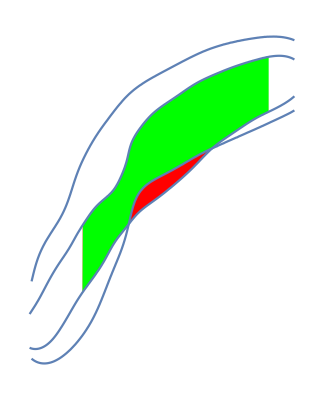
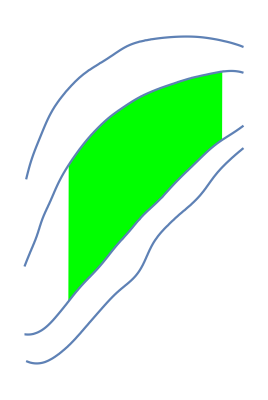

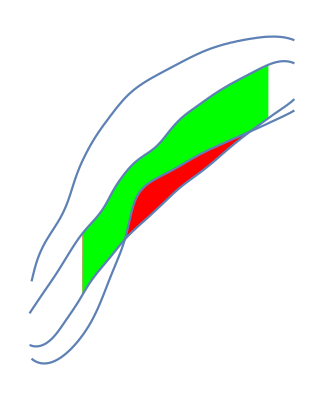
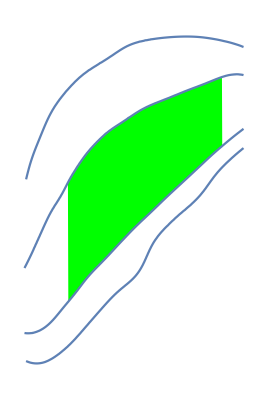

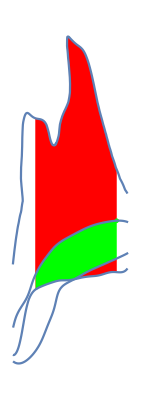

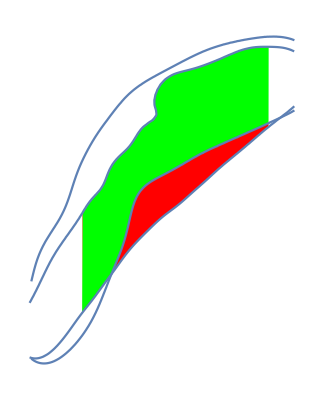
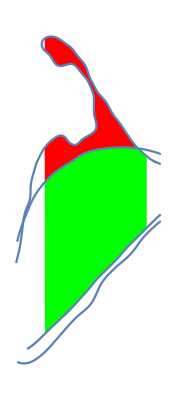

```mathematica
Show[rD[MONDRaw,#]/. Region[x__] :> Region[Style[x, Red] ], rI[MONDRaw,#]/. Region[x__] :> Region[Style[x, Green] ], plotMONDRawSigma[#], plotObsSigma[#]] & /@ {1,2}

Show[rD[MONDExp,#]/. Region[x__] :> Region[Style[x, Red] ], rI[MONDExp,#]/. Region[x__] :> Region[Style[x, Green] ], plotMONDExpSigma[#], plotObsSigma[#]] & /@ {1,2}

Show[rD[Palatini,#]/. Region[x__] :> Region[Style[x, Red] ], rI[Palatini,#]/. Region[x__] :> Region[Style[x, Green] ], plotPalatiniSigma[#], plotObsSigma[#]] & /@ {1}

Show[rD[RGGR,#]/. Region[x__] :> Region[Style[x, Red] ], rI[RGGR,#]/. Region[x__] :> Region[Style[x, Green] ], plotRGGRSigma[#], plotObsSigma[#]] & /@ {1,2}
```